## compressible n-H spheroid

### continuous ODEs

```mathematica
Ften=DiagonalMatrix[{r'[R],r[R]/R, r[R]/R}];
Gten=DiagonalMatrix[{γR[R],γθ[R],γθ[R]}];
Aten=Ften.Inverse[Gten];
Bten=Aten.Transpose[Aten];
I1=Tr[Transpose[Aten].Aten];
Id=IdentityMatrix[3];
```

```mathematica
W=μ/2(I1-3-2Log[Det[Aten]])+κ/2(Det[Aten]-1)^2+χ/2((Det[Gten]-1)/(Det[Gten]+1))^2;
Tten=μ/Det[Aten](Bten-Id)+κ (Det[Aten]-1)Id;
```

```mathematica
TRR:=Tten[[1,1]];
Tθθ:=Tten[[2,2]];
ΔT:=Tθθ-TRR
Ttemp:=DiagonalMatrix[{TR[R],TR[R]+ΔT, TR[R]+ΔT}]
Σtemp:={σ+ps,-1/2 σ+ps, -1/2 σ+ps}
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^-2(t-KillTime)]
RHS:=Diagonal[killAt[t,killGrowthTime](Det[Aten] Ttemp+Σtemp-W Id-(2 χ (-1+Det[Gten]) Det[Gten])/(1+Det[Gten])^3 Id(*-Det[Gten](((-1+Det[Gten]) χ)/Det[Gten]^3)Id*))][[1;;2]]
```

```mathematica
ODEdivT= TR'[R]==(2r'[R])/r[R] ΔT//FullSimplify (* stress balance div T = 0 *)
```

(2 R^2 μ γθ[R]^2 r'[R]^2)/(r[R]^3 γR[R])+TR'[R]==(2 μ γR[R])/r[R]

```mathematica
(* presented in the paper as follows: *)
Solve[ODEdivT, TR'[R]]/.μ->1//Together
```

{{TR'[R]→(2 (r[R]^2 γR[R]^2-R^2 γθ[R]^2 r'[R]^2))/(r[R]^3 γR[R])}}

```mathematica
ODErprime=TR[R]==TRR (* constitutive law *)
```

TR[R]==κ (-1+(r[R]^2 r'[R])/(R^2 γR[R] γθ[R]^2))+(R^2 μ γR[R] γθ[R]^2 (-1+r'[R]^2/γR[R]^2))/(r[R]^2 r'[R])

```mathematica
(* presented in the paper as follows: *)
ODErprime/.μ->1//Expand;
Collect[%, r'[R]]
```

TR[R]==-κ-(R^2 γR[R] γθ[R]^2)/(r[R]^2 r'[R])+((κ r[R]^2)/(R^2 γR[R] γθ[R]^2)+(R^2 γθ[R]^2)/(r[R]^2 γR[R])) r'[R]

```mathematica
Gten//Det
```

γR[R] γθ[R]^2

```mathematica
Ja[Pext_, κ_]:=Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]

Jg[Pext_,κ_ ]:=((√χ)/(√(-2  Ja[Pext, κ] Pext-2 ps+κ-2 Ja[Pext, κ] κ+Ja[Pext, κ]^2 κ-3 μ+3 Ja[Pext, κ]^(2/3) μ+χ-2 μ Log[Ja[Pext, κ]])))^1

psBoundary[Pext_,κ_ ]:=1/2 (κ+Ja[Pext, κ]^2 κ-2 Ja[Pext, κ] (Pext+κ)-3 μ+3 Ja[Pext, κ]^(2/3) μ+χ-2 μ Log[Ja[Pext, κ]])
```

### finite differences scheme

```mathematica
Δr:=B/(n-1);
```

```mathematica
subDiscrete:={r[R]->r[i][t], r'[R]->(r[i][t]-r[i-1][t])/Δr,TR[R]->TR[i][t], TR'[R]->(TR[i][t]-TR[i-1][t])/Δr,  R->i Δr, γR[R]->γR[i][t], γθ[R]->γθ[i][t], TR[n-1][t]->PextEvolution[t], r[0][t]->0};
subBC:={TR[n-1][t]->PextEvolution[t], r[0][t]->0}
```

```mathematica
BCs:=Table[{ODEdivT, ODErprime}/.subDiscrete/.i->ii,{ii,1, n-1}]/.subBC//Flatten;
```

```mathematica
ODEs:=Table[
Thread[{(γR[i]'[t])/(γR[i][t]),(γθ[i]'[t])/(γθ[i][t])}==ReplaceAll[RHS, subDiscrete]],{i, 1, n-1}]/.subBC//Flatten


ICs:=Flatten@Join[Table[{γR[i][0]==γθ[i][0]==(gInit+amp jsxs[i Δr]),  r[i][0]==(Ja[Pext, κ]^(1/3) gInit+amp jsxs[i Δr])  i Δr} , {i, 1, n-1}], Table[TR[i][0]==Pext,{i, 0, n-2}]];

vars:=Flatten@Join[Table[{γR[i],γθ[i], r[i]} , {i, 1, n-1}], Table[TR[i],{i, 0, n-2}]];
```

### get-functions

```mathematica
getER[tm_, sol_]:=Append[Table[{i Δr//N,-W + Det[Aten]TR[R]}/.subDiscrete/.subBC,{i, 1, n-2}],{(n-1) Δr//N, -W+Det[Aten] PextEvolution[tm]}/.subDiscrete/.i->n-1/.subBC]/.sol/.t->tm;
getEθ[tm_, sol_]:=Append[Table[{i Δr//N,-W + Det[Aten](TR[R]+ΔT)}/.subDiscrete/.subBC,{i, 1, n-2}],{(n-1) Δr//N,-W + Det[Aten](ΔT+PextEvolution[tm])}/.subDiscrete/.i->n-1/.subBC]/.sol/.t->tm;

getTR[tm_, sol_]:=Append[Table[{i Δr//N,TR[R]}/.subDiscrete/.subBC,{i, 1, n-2}],{(n-1) Δr//N, PextEvolution[tm]}/.subDiscrete/.i->n-1/.subBC]/.sol/.t->tm;
getTθ[tm_, sol_]:=Append[Table[{i Δr//N,(TR[R]+ΔT)}/.subDiscrete/.subBC,{i, 1, n-2}],{(n-1) Δr//N,ΔT+PextEvolution[tm]}/.subDiscrete/.i->n-1/.subBC]/.sol/.t->tm;

getγR[tm_, sol_]:=Table[{i Δr//N,γR[R]}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;
getγθ[tm_, sol_]:=Table[{i Δr//N,γθ[R]}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;
getDetG[tm_, sol_]:=Table[{i Δr//N,γR[R] γθ[R]^2}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;

getαR[tm_, sol_]:=Table[{R,r'[R]/γR[R]}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;
getαθ[tm_, sol_]:=Table[{R,(r[R]/R)/γθ[R]}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;
getDetA[tm_, sol_]:=Table[{R,r'[R]/γR[R]((r[R]/R)/γθ[R])^2}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;
getDensity[tm_, sol_]:=Table[{R,(r'[R]/γR[R]((r[R]/R)/γθ[R])^2)^-1}/.subDiscrete/.subBC,{i, 1, n-1}]/.sol/.t->tm;

getSizeExact[Pext_,κ_ ]:=Table[{tt,Ja[Pext,κ ] Jg[Pext,κ ] B^3/.t->tt },{tt, 0, tend,tend/200.0}];
getDetAExact[Pext_,κ_ ]:=Table[{i Δr//N,Ja[Pext,κ ]},{i, 1,n-2}];
getDetGExact[Pext_,κ_ ]:=Table[{i Δr//N,Jg[Pext,κ ]},{i, 1,n-2}];
getr[tm_, sol_]:=Prepend[Table[{i Δr//N,r[i][t]}/.subDiscrete/.subBC,{i, 1, n-2}],{0,0}]/.sol/.t->tm;

getSizeEvolution[ sol_]:=Table[{tt,(r[n-1][t])^3/.sol/.t->tt },{tt, 0, tend,tend/200.0}];
```

### Homogeneous solutions and size control boundaries rhsUpper, rhsLower

```mathematica
subHom={γR[R]->Jg^(1/3), γθ[R]->Jg^(1/3), r->Function[R,Ja^(1/3) Jg^(1/3)  R]};
```

```mathematica
{ ODEdivT, ODErprime}/.subHom//FullSimplify
```

{TR'[R]==0,TR[R]==(-1+Ja) κ+((-1+Ja^(2/3)) μ)/Ja}

```mathematica
(* Define Ja by solving the following equation *)
(*
First@Solve[ODErprime/.subHom, TR[R]]//FullSimplify
Pext==TR[R]/.%//FullSimplify
Solve[%, Ja][[2]]/.{μ->1(*, Pext->-0.1, κ->0.1*)}//FullSimplify
*)
Ja[Pext_, κ_]:=Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]
```

```mathematica
f[Jg_]:=((Jg-1)/(Jg+1))^2
```

```mathematica
(* full case *)
(* ps-W+Ja Pext-χ/2 f'[Jg]Jg/.subHom/.Ja->Ja[Pext,κ] *)
```

```mathematica
rhsFull[Jg_,ps_, χ_, Pext_,μ_, κ_ ]:=ps-((-1+Jg)^2 χ)/(2 (1+Jg)^2)-1/2 Jg (-(2 (-1+Jg)^2)/(1+Jg)^3+(2 (-1+Jg))/(1+Jg)^2) χ-1/2 μ (-3-2 Log[Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]]+3 Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]^(2/3))-1/2 κ (-1+Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2])^2+Pext Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]
```

```mathematica
rhsFull[Jg,ps, χ,0, 0, 0 ]==ps-χ/2 f[Jg]-Jg χ/2 f'[Jg]
```

True

```mathematica
ps-χ/2 f[Jg]-Jg χ/2 f'[Jg]
```

ps-((-1+Jg)^2 χ)/(2 (1+Jg)^2)-1/2 Jg (-(2 (-1+Jg)^2)/(1+Jg)^3+(2 (-1+Jg))/(1+Jg)^2) χ

```mathematica
(* upper bound *)
(* ps-W+Ja Pext-χ/2 f'[Jg]Jg/.subHom/.Ja->Ja[Pext,κ]/.Jg->1/2//FullSimplify *)
```

```mathematica
rhsUpper[ps_, χ_, Pext_,μ_, κ_ ]:=ps+(5 χ)/54+1/2 μ (3+2 Log[Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]]-3 Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]^(2/3))-1/2 κ (-1+Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2])^2+Pext Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]
```

```mathematica
(* lower bound *)
(* ps-W+Ja Pext-χ/2 f'[Jg]Jg/.subHom/.Ja->Ja[Pext,κ]/.Jg->0//FullSimplify *)
```

```mathematica
rhsLower[ps_, χ_, Pext_,μ_, κ_ ]:=ps-χ/2+1/2 μ (3+2 Log[Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]]-3 Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]^(2/3))-1/2 κ (-1+Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2])^2+Pext Root[-1+(-3 Pext-3 κ) #1+(1-3 Pext^2+3 κ-6 Pext κ-3 κ^2) #1^2+(-Pext^3+6 Pext κ-3 Pext^2 κ+6 κ^2-3 Pext κ^2-κ^3) #1^3+(3 Pext^2 κ-3 κ^2+6 Pext κ^2+3 κ^3) #1^4+(-3 Pext κ^2-3 κ^3) #1^5+κ^3 #1^6&,2]
```

### Noise profiles

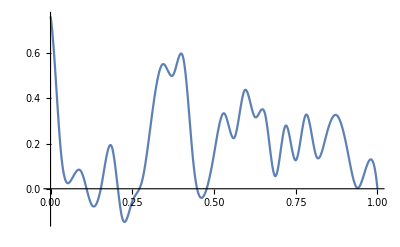

```mathematica
(* STX question: "Generate a smooth random function (2D curve) with endpoints specification?" *)

BlockRandom[(*for reproducibility*)SeedRandom["somefunction",Method->"MersenneTwister"];
jsxsClassic=Interpolation[MapAt[Rescale[#,{0,2},{-1,1}]&,RandomFunction[BrownianBridgeProcess[0,2],{0,2,1/32}]["Path"],{All,1}],Method->"Spline"]];
Plot[jsxsClassic[x],{x,0,1}]
```

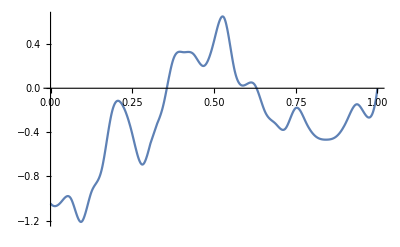

```mathematica
BlockRandom[(*for reproducibility*)SeedRandom["RA",Method->"MersenneTwister"];
jsxs2=Interpolation[MapAt[Rescale[#,{0,2},{-1,1}]&,RandomFunction[BrownianBridgeProcess[0,2],{0,2,1/32}]["Path"],{All,1}],Method->"Spline"]];
Plot[jsxs2[x],{x,0,1}]
```

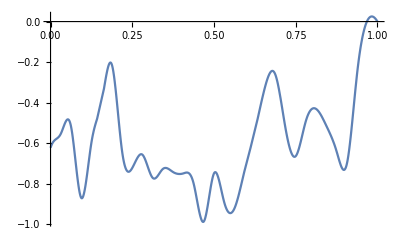

```mathematica
BlockRandom[(*for reproducibility*)SeedRandom["ALBERT",Method->"MersenneTwister"];
jsxs3=Interpolation[MapAt[Rescale[#,{0,2},{-1,1}]&,RandomFunction[BrownianBridgeProcess[0,2],{0,2,1/32}]["Path"],{All,1}],Method->"Spline"]];
Plot[jsxs3[x],{x,0,1}]
```

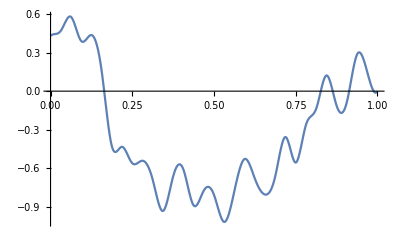

```mathematica
BlockRandom[(*for reproducibility*)SeedRandom["ukraine",Method->"MersenneTwister"];
jsxs4=Interpolation[MapAt[Rescale[#,{0,2},{-1,1}]&,RandomFunction[BrownianBridgeProcess[0,2],{0,2,1/32}]["Path"],{All,1}],Method->"Spline"]];
Plot[jsxs4[x],{x,0,1}]
```

### color scheme & cosmetics

```mathematica
is=300;
bs=15;
```

```mathematica
ColorMapSuitePath=NotebookDirectory[]<>"ScientificColourMaps7";
ColorMapSuite[name_String]:=ColorMapSuite[name,-1]
ColorMapSuite[name_String,el_]:=With[{list=Transpose@{Subdivide[0,1,255],RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]}},Blend[list,{##}[[el]]]&]
```

```mathematica
colZeroOne=ColorMapSuite["berlin"];
```

```mathematica
(* generated with: ColorMapSuite["batlow"] *)
```

```mathematica
bartlowColList={{0,RGBColor[0.005193153367084745, 0.0982381170217676, 0.3498418809830899]},{1/255,RGBColor[0.00906521459033197, 0.1044866508299995, 0.3509330851973159]},{2/255,RGBColor[0.012963349842328881, 0.11077922487868916, 0.3519924367491822]},{1/85,RGBColor[0.016529926949735135, 0.11691328972102498, 0.35306965300420096]},{4/255,RGBColor[0.0199356188871784, 0.12298460990134438, 0.354119746868454]},{1/51,RGBColor[0.02318878486087881, 0.12903519373149894, 0.3551824331392611]},{2/85,RGBColor[0.02629125326861058, 0.13504437659330928, 0.35621017793577603]},{7/255,RGBColor[0.029245489023060157, 0.14096397126160432, 0.3572385444087573]},{8/255,RGBColor[0.03205278397327522, 0.14677416313591207, 0.3582388098645774]},{3/85,RGBColor[0.0348531921361111, 0.15255833701528124, 0.35923261671019346]},{2/51,RGBColor[0.037449120197873095, 0.15831302906694084, 0.36021587390047566]},{11/255,RGBColor[0.03984508507773596, 0.16397782635415398, 0.36118714532095]},{4/85,RGBColor[0.042104481436739956, 0.16955702528601388, 0.3621513500244556]},{13/255,RGBColor[0.044069304939279935, 0.17505286745845028, 0.3630835172211513]},{14/255,RGBColor[0.04590454177718842, 0.18045998148098763, 0.36400713889938585]},{1/17,RGBColor[0.04766491552117986, 0.18584438525797461, 0.3649146027045783]},{16/255,RGBColor[0.04937771055294349, 0.19107609466670547, 0.3658097737930779]},{1/15,RGBColor[0.05079491453572351, 0.196274189099404, 0.3666843178291345]},{6/85,RGBColor[0.05216442261319991, 0.2013231093466841, 0.36752442884120756]},{19/255,RGBColor[0.05347060931723789, 0.2063572173160873, 0.3683703215416836]},{4/51,RGBColor[0.05472081902680487, 0.2112336395043889, 0.36918391837772296]},{7/85,RGBColor[0.055927956548658966, 0.21604632568493123, 0.36997350072132634]},{22/255,RGBColor[0.057033202888293694, 0.22075440398869803, 0.3707499592314271]},{23/255,RGBColor[0.05803215940134297, 0.22533951277498812, 0.37150894575967397]},{8/85,RGBColor[0.05916444726331392, 0.22984235549248522, 0.372251954677445]},{5/51,RGBColor[0.06016698490666767, 0.23429914210561742, 0.37297805178168253]},{26/255,RGBColor[0.06105185290468469, 0.23862497540933905, 0.3736914837038787]},{9/85,RGBColor[0.062059916945595046, 0.24288791613647467, 0.3743860360063075]},{28/255,RGBColor[0.06307118851928215, 0.2470851847296836, 0.3750497628325021]},{29/255,RGBColor[0.06398207456277889, 0.25121343878467817, 0.37570881789396715]},{2/17,RGBColor[0.06493599599964549, 0.2552641171581149, 0.3763622349015682]},{31/255,RGBColor[0.06590265590094782, 0.2592565304078538, 0.37698716945665117]},{32/255,RGBColor[0.06689896495473623, 0.26318767055475906, 0.37759435604864444]},{11/85,RGBColor[0.06792124382248342, 0.2670556655025555, 0.3781911660208122]},{2/15,RGBColor[0.06900153992680301, 0.2709216996688603, 0.37877419717350214]},{7/51,RGBColor[0.07000086742222131, 0.27471269540286414, 0.3793420661303846]},{12/85,RGBColor[0.07111497011170888, 0.2784970788777719, 0.3798949405899265]},{37/255,RGBColor[0.07219238852229261, 0.2822485923666056, 0.38043438237196786]},{38/255,RGBColor[0.07344021874372691, 0.2859415755335133, 0.38095684875304925]},{13/85,RGBColor[0.07459477631965121, 0.2896534758224459, 0.38145245097980185]},{8/51,RGBColor[0.07583316231246431, 0.29332080890607, 0.3819221265171391]},{41/255,RGBColor[0.07713575086677539, 0.2969956198895208, 0.3823762561756469]},{14/85,RGBColor[0.0785169378778106, 0.30062163288111604, 0.3828141416419706]},{43/255,RGBColor[0.07998408549785488, 0.3042521172826271, 0.38322375648442114]},{44/255,RGBColor[0.08155250132784678, 0.307858398947125, 0.38359755116259286]},{3/17,RGBColor[0.08308211730214995, 0.3114607306136936, 0.3839360907891627]},{46/255,RGBColor[0.08477795683248569, 0.31504326897178137, 0.38423959035577426]},{47/255,RGBColor[0.08650289890409021, 0.31861526671309764, 0.38450584864340215]},{16/85,RGBColor[0.08835319612192202, 0.32216699518938113, 0.3847307176551048]},{49/255,RGBColor[0.09028134532757431, 0.32568540525004724, 0.3849100143661224]},{10/51,RGBColor[0.09230383456624085, 0.3292197629083868, 0.3850396573239535]},{1/5,RGBColor[0.09446213251316372, 0.3327116897085504, 0.38511560668427935]},{52/255,RGBColor[0.09661809539832363, 0.3361614658561598, 0.3851338100463711]},{53/255,RGBColor[0.09901532267195258, 0.3396206396804419, 0.3850901717224934]},{18/85,RGBColor[0.10148075503464712, 0.3430356886142494, 0.3849805699006658]},{11/51,RGBColor[0.10407782175559886, 0.34640951437135353, 0.3848009521540483]},{56/255,RGBColor[0.1068415417894461, 0.3497740690589232, 0.38454754507201544]},{19/85,RGBColor[0.10969518137400697, 0.3530981978863, 0.3842172172502675]},{58/255,RGBColor[0.1126548905811111, 0.35639097599502095, 0.3838073118712301]},{59/255,RGBColor[0.11574804299976826, 0.3596382790196865, 0.3833102355268599]},{4/17,RGBColor[0.11899185226757944, 0.36284860147640574, 0.38271289196822167]},{61/255,RGBColor[0.12232007085416291, 0.36603048313988734, 0.38202555689973977]},{62/255,RGBColor[0.12588949580950715, 0.36915956033350067, 0.38125939910510814]},{21/85,RGBColor[0.12951895278986603, 0.37223835820701584, 0.3803775977485293]},{64/255,RGBColor[0.13329781036453003, 0.3752817757604749, 0.3793954095265211]},{13/51,RGBColor[0.13721217317778236, 0.37828228973598077, 0.3783146416765613]},{22/85,RGBColor[0.14125972272499474, 0.3812395532769262, 0.37713457767678255]},{67/255,RGBColor[0.1454320711465689, 0.3841301461158962, 0.375839810714344]},{4/15,RGBColor[0.14970605921174326, 0.3869750464356994, 0.37444878673936705]},{23/85,RGBColor[0.15407297935142533, 0.38977720239248426, 0.3729339734772393]},{14/51,RGBColor[0.1586196382745385, 0.39253083557636365, 0.3713202601014282]},{71/255,RGBColor[0.1632459417074294, 0.395237177909865, 0.3696085079279714]},{24/85,RGBColor[0.1679516304435099, 0.3978894758325473, 0.36778403427924616]},{73/255,RGBColor[0.1727876722265655, 0.40049616579948016, 0.3658673178915559]},{74/255,RGBColor[0.1777520242325257, 0.4030413243185383, 0.36383253544698607]},{5/17,RGBColor[0.18273184630080283, 0.4055506422670725, 0.3617139812207053]},{76/255,RGBColor[0.18788592197876566, 0.4080032201407193, 0.35948448768180946]},{77/255,RGBColor[0.19305035570120452, 0.4104274433814088, 0.357176852635486]},{26/85,RGBColor[0.19830954704068637, 0.41279752713983114, 0.35476654101062277]},{79/255,RGBColor[0.20367609961813737, 0.41511601961326783, 0.35225256863459553]},{16/51,RGBColor[0.2090752388963242, 0.417412080725871, 0.3496767296453781]},{27/85,RGBColor[0.2145549096303504, 0.4196610314623223, 0.3470186694612174]},{82/255,RGBColor[0.22011194218117586, 0.4218641753656316, 0.3442611096338137]},{83/255,RGBColor[0.22570724370731254, 0.4240494459079223, 0.3414592049007958]},{28/85,RGBColor[0.23136234768511588, 0.4261974566798758, 0.3385720498359743]},{1/3,RGBColor[0.23707454607405365, 0.42832460818730694, 0.33563448126966455]},{86/255,RGBColor[0.2427949464944569, 0.43041813391463224, 0.3326345960882581]},{29/85,RGBColor[0.24861685995293464, 0.4324925668390824, 0.32957115867044184]},{88/255,RGBColor[0.25445231948078745, 0.43452908459242406, 0.32643417320075546]},{89/255,RGBColor[0.26031994501761613, 0.4365563804621614, 0.32328504095856714]},{6/17,RGBColor[0.26624103559495926, 0.438555352552268, 0.32008520332780216]},{91/255,RGBColor[0.2721682175019895, 0.44054125389534415, 0.31683077060365905]},{92/255,RGBColor[0.278171063633642, 0.44252433547295505, 0.3135517021145336]},{31/85,RGBColor[0.2841746060485501, 0.444483674290572, 0.3102427986785198]},{94/255,RGBColor[0.29021386560947077, 0.44642003736878627, 0.3068891773422693]},{19/51,RGBColor[0.296294199927995, 0.44835650967502766, 0.3035090897309069]},{32/85,RGBColor[0.3023785627690957, 0.4502815737212346, 0.30012236213619936]},{97/255,RGBColor[0.3085168891831788, 0.4522047620736407, 0.2967207888227706]},{98/255,RGBColor[0.314648370646325, 0.45410714049204104, 0.29327876318162127]},{33/85,RGBColor[0.32083356948444874, 0.45600557022948207, 0.28984099298915933]},{20/51,RGBColor[0.32700657046640985, 0.45790041408363436, 0.28637653338724006]},{101/255,RGBColor[0.3332347824546288, 0.4597940016053313, 0.2829372045776807]},{2/5,RGBColor[0.33946912341713625, 0.4616845703169037, 0.27946782286049837]},{103/255,RGBColor[0.34570343690782523, 0.4635628994601804, 0.2759984508047391]},{104/255,RGBColor[0.3519760378874838, 0.46544005687368395, 0.27249229457065943]},{7/17,RGBColor[0.3582770919960637, 0.4673313629822978, 0.2690369839639225]},{106/255,RGBColor[0.3645890255190674, 0.4692131045104409, 0.2655434834600164]},{107/255,RGBColor[0.37092238495526125, 0.4710853389235179, 0.26206384364450047]},{36/85,RGBColor[0.37729103199175273, 0.47295177298973484, 0.25858753735262613]},{109/255,RGBColor[0.38367513341047843, 0.47484167257792465, 0.2551314964878732]},{22/51,RGBColor[0.3900701662780218, 0.47671078250738447, 0.2516645567489511]},{37/85,RGBColor[0.39650491134072274, 0.478587417929165, 0.24821214442162315]},{112/255,RGBColor[0.4029676055462818, 0.48046597848254047, 0.24473116161388492]},{113/255,RGBColor[0.40945476550362553, 0.48235070950586556, 0.2413137980167112]},{38/85,RGBColor[0.41596738524987337, 0.4842252855409939, 0.23789477741620474]},{23/51,RGBColor[0.42250697989767744, 0.48611298304515793, 0.23449349835575795]},{116/255,RGBColor[0.4290943832351661, 0.48801065150519185, 0.23109635675825485]},{39/85,RGBColor[0.43571356939928224, 0.48989049128592926, 0.22772839964768413]},{118/255,RGBColor[0.4423653391272914, 0.49179535392211904, 0.22435367889204286]},{7/15,RGBColor[0.44905189106053267, 0.4936844329051522, 0.2210735495141634]},{8/17,RGBColor[0.4557739000068354, 0.4955846774693378, 0.2177743551480794]},{121/255,RGBColor[0.46253874114016624, 0.49749734629405706, 0.21451784464324958]},{122/255,RGBColor[0.4693681759290078, 0.49939268549601173, 0.2113176200553523]},{41/85,RGBColor[0.4762206870336379, 0.5013143526201598, 0.20814844431926055]},{124/255,RGBColor[0.48312282972791437, 0.5032161985929168, 0.2050370497105667]},{25/51,RGBColor[0.49008113315162144, 0.505136594492485, 0.20197616140253158]},{42/85,RGBColor[0.4970888484076958, 0.5070578325218741, 0.19899427513028659]},{127/255,RGBColor[0.5041533676300165, 0.5089839552242211, 0.1961180358880897]},{128/255,RGBColor[0.5112531863663102, 0.5108978758437912, 0.19329557161683117]},{43/85,RGBColor[0.5184248173778219, 0.512821529411328, 0.19056640501529096]},{26/51,RGBColor[0.5256367015730944, 0.5147464059492216, 0.1879899267243815]},{131/255,RGBColor[0.5329068086225821, 0.5166619744455649, 0.18549690227149584]},{44/85,RGBColor[0.5402253388010938, 0.5185841721042183, 0.183099222034565]},{133/255,RGBColor[0.5475992962429519, 0.5204856109898492, 0.18088362883209758]},{134/255,RGBColor[0.5550237443515474, 0.5223907588063386, 0.17885366268168976]},{9/17,RGBColor[0.5625064466329394, 0.5242926175482936, 0.17696406966511063]},{8/15,RGBColor[0.5700155866011719, 0.526185875241075, 0.17527272145547185]},{137/255,RGBColor[0.5775820075373922, 0.5280581946778243, 0.17377468823395817]},{46/85,RGBColor[0.5851991583363613, 0.529926872028961, 0.17249347219852024]},{139/255,RGBColor[0.5928461933161586, 0.531776970655186, 0.1714486909855958]},{28/51,RGBColor[0.6005204120803953, 0.5336045490746475, 0.1706478010371041]},{47/85,RGBColor[0.6082399039723267, 0.5354230972332484, 0.1701044984943837]},{142/255,RGBColor[0.6159723223277639, 0.537231237632357, 0.16982607466873542]},{143/255,RGBColor[0.6237390014494381, 0.5390018446915938, 0.1698137589611198]},{48/85,RGBColor[0.6315126979581867, 0.540752449196533, 0.17007475185076026]},{29/51,RGBColor[0.6393009011315247, 0.5424838668737295, 0.17062230362745182]},{146/255,RGBColor[0.6470984735516427, 0.544182954477616, 0.17146485486178015]},{49/85,RGBColor[0.6548888941695018, 0.5458628473132509, 0.1726026959666576]},{148/255,RGBColor[0.6626912095384206, 0.5475028509940739, 0.1740441636457403]},{149/255,RGBColor[0.6704773987252629, 0.5491267899660764, 0.17574652837600505]},{10/17,RGBColor[0.6782435057902289, 0.5507118318166707, 0.1778028254107114]},{151/255,RGBColor[0.6859952053971045, 0.5522742763898049, 0.18005620349514892]},{152/255,RGBColor[0.6937199105780304, 0.5537967644647263, 0.18261027740926]},{3/5,RGBColor[0.7014210764661721, 0.555294295332478, 0.1854782436820058]},{154/255,RGBColor[0.7090976078519717, 0.5567715939382857, 0.18854636296542707]},{31/51,RGBColor[0.7167311958055946, 0.5582045138460956, 0.19185050359319988]},{52/85,RGBColor[0.7243222900273982, 0.5596276419797932, 0.195408149901273]},{157/255,RGBColor[0.7318779387297203, 0.5610109219258725, 0.1991738628703049]},{158/255,RGBColor[0.7393926057932174, 0.5623855177731327, 0.2031790194464354]},{53/85,RGBColor[0.7468501954483325, 0.563725389331799, 0.2073749396801499]},{32/51,RGBColor[0.7542682881292884, 0.5650332333700621, 0.211760789638594]},{161/255,RGBColor[0.7616287570461876, 0.56634373852435, 0.21632152690982306]},{54/85,RGBColor[0.7689417224250781, 0.5676303553824138, 0.22104513938190246]},{163/255,RGBColor[0.7762077315490165, 0.5688987878865995, 0.22593008933931036]},{164/255,RGBColor[0.783415838135567, 0.570161596146816, 0.23096169818099238]},{11/17,RGBColor[0.7905682832351899, 0.5714208480911801, 0.2361601998364352]},{166/255,RGBColor[0.7976654656247937, 0.572681501867017, 0.24149026342353114]},{167/255,RGBColor[0.8047092634538952, 0.5739278888467948, 0.24695529863841975]},{56/85,RGBColor[0.8116922177076217, 0.5751866844364272, 0.2525717360585131]},{169/255,RGBColor[0.818610222189201, 0.576461604502418, 0.25830322983908005]},{2/3,RGBColor[0.8254723451653395, 0.5777251816245221, 0.26419650676207984]},{57/85,RGBColor[0.8322721663406366, 0.5790257300386646, 0.27021114257162154]},{172/255,RGBColor[0.8389991521388886, 0.5803391491025478, 0.27635326813894934]},{173/255,RGBColor[0.8456567488069453, 0.5816715995111611, 0.2826305092206305]},{58/85,RGBColor[0.8522469835603281, 0.5830374368453031, 0.28903585603952037]},{35/51,RGBColor[0.858747197113258, 0.5844403255814892, 0.2955720385448463]},{176/255,RGBColor[0.8651682242450994, 0.5858818592158386, 0.30225470431144724]},{59/85,RGBColor[0.8715052658413278, 0.5873517848326715, 0.30911177602918927]},{178/255,RGBColor[0.8777410037249749, 0.5888734340157754, 0.3160811744866095]},{179/255,RGBColor[0.8838779664462431, 0.5904499325689858, 0.32319477087540505]},{12/17,RGBColor[0.8898997905034719, 0.5920866486650908, 0.3304540775020741]},{181/255,RGBColor[0.8958093313609026, 0.5937651010776226, 0.3378653498224334]},{182/255,RGBColor[0.9015904177259412, 0.5955074054444204, 0.3454288544909969]},{61/85,RGBColor[0.9072416855607618, 0.5973189263808381, 0.35314225470189153]},{184/255,RGBColor[0.9127463125086187, 0.5991911996824932, 0.3609864487033381]},{37/51,RGBColor[0.9181026804280301, 0.6011258270443951, 0.3689989740040986]},{62/85,RGBColor[0.9232998659240212, 0.6031373399712203, 0.3771387071173142]},{11/15,RGBColor[0.9283232091535554, 0.6052123838148247, 0.3854044343356354]},{188/255,RGBColor[0.9331757063345633, 0.60736895111811, 0.39381661712976285]},{63/85,RGBColor[0.9378496742980906, 0.6095816814207388, 0.402345183479063]},{38/51,RGBColor[0.942331841620567, 0.6118673492779588, 0.41100643836430095]},{191/255,RGBColor[0.9466116954773739, 0.6142184936872118, 0.4197671190995584]},{64/85,RGBColor[0.9506969673003716, 0.6166487438332956, 0.42862417218014814]},{193/255,RGBColor[0.9545735519415848, 0.6191372742405447, 0.43758222343689757]},{194/255,RGBColor[0.9582441631443231, 0.6216712178297037, 0.4466038994114542]},{13/17,RGBColor[0.9616963227638149, 0.6242822966856691, 0.45570178224399416]},{196/255,RGBColor[0.9649427508668024, 0.6269343546666735, 0.4648597210220807]},{197/255,RGBColor[0.9679827294109881, 0.6296391000418288, 0.4740571569355506]},{66/85,RGBColor[0.9708041934518005, 0.6323937061133272, 0.4832897189513224]},{199/255,RGBColor[0.9734236573646047, 0.6351829029011401, 0.49254690556271924]},{40/51,RGBColor[0.9758353864153829, 0.6380119755078629, 0.5018263821793786]},{67/85,RGBColor[0.9780522878867093, 0.6408681647557488, 0.511089790326883]},{202/255,RGBColor[0.9800792836396328, 0.6437519005347476, 0.520349963396144]},{203/255,RGBColor[0.9819179053428766, 0.6466637495214104, 0.5296023025308836]},{4/5,RGBColor[0.9835737566710987, 0.6495902217676868, 0.5388187306681658]},{41/51,RGBColor[0.9850658742908114, 0.6525215673894564, 0.5479984637725441]},{206/255,RGBColor[0.9863924535985507, 0.6554702952779925, 0.5571416685019798]},{69/85,RGBColor[0.9875668406547834, 0.6584217185210594, 0.5662264160947723]},{208/255,RGBColor[0.9885958122187206, 0.6613777963728396, 0.5752646372935034]},{209/255,RGBColor[0.9894964040732597, 0.664328686022486, 0.5842462268216205]},{14/17,RGBColor[0.99026761260722, 0.6672804641856739, 0.5931735541637225]},{211/255,RGBColor[0.990925532131, 0.6702301975007446, 0.6020305430034925]},{212/255,RGBColor[0.9914785301882021, 0.6731646593428352, 0.6108351051068914]},{71/85,RGBColor[0.991935238397665, 0.6760909921006679, 0.6195754855710046]},{214/255,RGBColor[0.9923046658887763, 0.6790071219427478, 0.6282512775397422]},{43/51,RGBColor[0.9925948391586693, 0.6819138828242806, 0.6368692956942783]},{72/85,RGBColor[0.9928132750814979, 0.6848154745222541, 0.6454230424726428]},{217/255,RGBColor[0.9929674063249064, 0.6877053160266439, 0.6539344520718204]},{218/255,RGBColor[0.9930643099690208, 0.69057891865392, 0.6623980338874967]},{73/85,RGBColor[0.9931105441159147, 0.6934513233405696, 0.6708104867091674]},{44/51,RGBColor[0.9931120849921747, 0.6963137745202373, 0.6791772587254299]},{13/15,RGBColor[0.9930743221588754, 0.6991606001856622, 0.6875192645539461]},{74/85,RGBColor[0.9930020839259176, 0.7020063414676727, 0.6958314440915181]},{223/255,RGBColor[0.9928996757060824, 0.7048518670395225, 0.7041140144806634]},{224/255,RGBColor[0.9927709213388299, 0.7076892230192429, 0.7123800157834812]},{15/17,RGBColor[0.9926192024586513, 0.7105300216242687, 0.7206385642501894]},{226/255,RGBColor[0.9924474941324879, 0.7133656158772053, 0.7288915461909581]},{227/255,RGBColor[0.9922583962864815, 0.7162098672692777, 0.7371455146895275]},{76/85,RGBColor[0.992054154948831, 0.7190487099910903, 0.7454025842160593]},{229/255,RGBColor[0.9918365767308647, 0.7218926255124882, 0.7536734578479803]},{46/51,RGBColor[0.9916070333456365, 0.7247542962769521, 0.7619588693287709]},{77/85,RGBColor[0.9913665497308912, 0.7276136928455845, 0.7702698492305938]},{232/255,RGBColor[0.9911158331193111, 0.7304893697597771, 0.7786056353198485]},{233/255,RGBColor[0.9908553786637279, 0.7333733724007395, 0.7869758989063456]},{78/85,RGBColor[0.9905855597323155, 0.7362648403784187, 0.7953708139956405]},{47/51,RGBColor[0.9903065510455036, 0.7391843624833386, 0.8038097534534149]},{236/255,RGBColor[0.9900183036533058, 0.7421024656402168, 0.8122852661755257]},{79/85,RGBColor[0.9897201605469811, 0.7450391977175737, 0.8208041269437343]},{14/15,RGBColor[0.9894109601229567, 0.7479973041832442, 0.8293723776254878]},{239/255,RGBColor[0.9890892793449574, 0.7509682178760204, 0.8379786653074179]},{16/17,RGBColor[0.9887543759571258, 0.753949469054436, 0.8466273512151431]},{241/255,RGBColor[0.9884064969216979, 0.7569487779511263, 0.8553321380307732]},{242/255,RGBColor[0.9880460056954711, 0.7599636517823959, 0.8640778366211941]},{81/85,RGBColor[0.9876715115468123, 0.7629956264742592, 0.8728641334807893]},{244/255,RGBColor[0.9872798590258427, 0.7660469341106407, 0.8816985891558072]},{49/51,RGBColor[0.9868679281152041, 0.7691045891720196, 0.8905725851461087]},{82/85,RGBColor[0.9864347952465548, 0.772184129460011, 0.8994929672526742]},{247/255,RGBColor[0.9859802453546757, 0.7752724373756446, 0.908448239797334]},{248/255,RGBColor[0.985503244682332, 0.7783778749992695, 0.9174441659006735]},{83/85,RGBColor[0.9850020679635899, 0.781495470778951, 0.9264677968127821]},{50/51,RGBColor[0.9844732958366768, 0.7846241807523092, 0.9355310621283563]},{251/255,RGBColor[0.9839125936007757, 0.787756858655277, 0.9446261751501791]},{84/85,RGBColor[0.9833215511973703, 0.7909054211529133, 0.9537480969728521]},{253/255,RGBColor[0.9827025890474234, 0.7940679805757733, 0.962895385102887]},{254/255,RGBColor[0.9820478068811576, 0.7972279484156861, 0.9720703858073826]},{1,RGBColor[0.9813535753006561, 0.8004061671470218, 0.9812666660455576]}};
```

```mathematica
bartlowColListReversed=Transpose@{bartlowColList[[All, 1]],Reverse@bartlowColList[[All, 2]]};
```

```mathematica
batlowBlend=Blend[bartlowColListReversed,{##1}⟦-1⟧]&;
```

## Size control boundary

### Setup

```mathematica
size[psP_]:=Module[{res},
ps=psP;
res=Jg[t]/.solReduced[0.5]/.t->tend;
Clear[ps];
res

]
```

```mathematica
eqn:=Jg'[t]/Jg[t] ==ReplaceAll[ps-W+Ja Pext-χ/2 f'[Jg]Jg/.subHom,{ Jg->Jg[t], Ja->Ja[Pext,κ] }]//N;

solReduced[Jg0_]:=First@NDSolve[{eqn, Jg[0]==Jg0},Jg[t], {t, 0, tend}]
```

```mathematica
(* presenting RHS like in the paper *)
rhs=ps-W+Ja Pext-χ/2 f'[Jg]Jg/.subHom/.μ->1;
hpaper=Coefficient[rhs, χ]//FullSimplify (* term called h in the paper *)
cpaper=rhs-ps-hpaper χ//FullSimplify (* term called c in the paper *)

rhs==ps + hpaper χ + cpaper//FullSimplify
```

-1/2-4/(1+Jg)^3+4/(1+Jg)^2

1/2 (3-3 Ja^(2/3)+2 Ja Pext-(-1+Ja)^2 κ+2 Log[Ja])

True

### No mechanical feedback

```mathematica
Clear@ps
InsetPlot[ps_]:=Module[{},
is=105;
bs=11;
Plot[rhsFull[Jg,ps, χ, Pext,μ, κ ]//Evaluate,{Jg, 0,8}, PlotRange->{All,1.1{-1,1.3}}, ImageSize->is, BaseStyle->bs, PlotTheme->"Scientific", AspectRatio->1.75, FrameStyle->Black,  FrameLabel->{"|𝔾|", None},PlotStyle->Directive[Blue], PlotLegends->Placed[{"|OverHat[𝔾̇]||𝔾|^-1"} , {Right,If[True,  Top, Bottom]}]]];
```

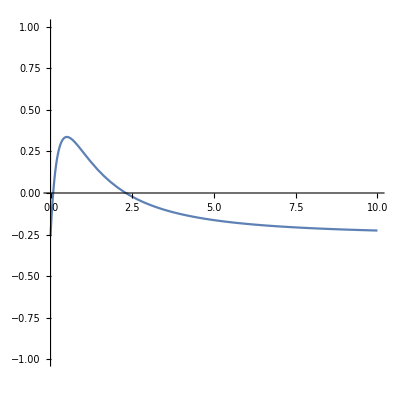

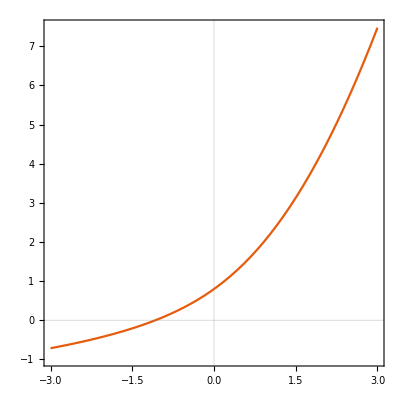

```mathematica
(* parameter values used in paper *)
(* rhsFull[Jg,ps, χ, Pext,μ, κ ] *)

Plot[rhsFull[Jg,1, 1,-1,1,1 ],{Jg,0, 10 }, PlotRange->{All, {-1,1}}, AspectRatio->1]

Plot[rhsFull[2,1, 1,Pext,1,1 ],{Pext, -3, 3}, PlotRange->{{-3, 3}, {-1, 7.5}}, PlotTheme->"Scientific", AspectRatio->1]
```

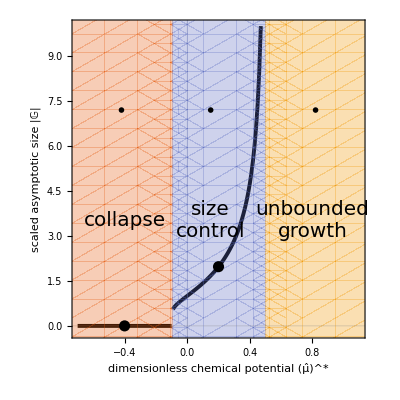

```mathematica
χ=1;
tend=100;
Pext=0;
μ=0;
κ=0;
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];

list={#,size[#]}&/@{0.2,0.8, -0.4 };


InsetStable=InsetPlot[0.2];
InsetExp=InsetPlot[0.8];
InsetZero=InsetPlot[-0.4];


RP=RegionPlot[{ps<lowerPsbound,lowerPsbound<ps<upperPsbound, ps>upperPsbound},{ps, -2, 2},{size, -1, 11}, PlotTheme->"Scientific", BoundaryStyle->None];

PP=ListPlot[{list}, PlotStyle->Directive[Black, PointSize[0.02]]];

is= 400;
bs=17;
heigthCoordinate=7.2;
data=Table[{pss,size[pss]},{pss, -0.7,1.1, 0.01}];
LP=ListPlot[{Select[data, #[[2]]<0.2&], Select[data, #[[2]]>0.2&]}, PlotRange->{All,{-0.2, 10}}, PlotStyle->Directive[Black, Thickness[0.007]], Joined->True, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, FrameLabel->{"dimensionless chemical potential (μ̂)^*", "scaled asymptotic  size |𝔾|"}, Epilog->{Inset[InsetStable,{0.15, heigthCoordinate}], Inset[InsetExp,{0.82, heigthCoordinate}],  Inset[InsetZero,{-0.42,heigthCoordinate}], Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.15,3.5}], Inset[Style["collapse", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{-0.4,3.5}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.8,3.5}]}, Background->White];

Show[LP, RP, PP]
```

### Plots

```mathematica
is= 430;
bs=17;
Jgrange=10;
μrange=8;

Pext=-1;
 μ=1;
κ=1;
Clear[ps, χ];

CP=ContourPlot[{rhsLower[ps, χ, Pext,μ, κ ]==0, rhsUpper[ps, χ, Pext,μ, κ ]==0}//Evaluate,{ps, 0, μrange}, {χ, 0, μrange}, PlotTheme->"Scientific", BaseStyle->bs, FrameStyle->Black, ContourStyle->Directive[Dashed, Gray],FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}, ImageSize->is];


RP = RegionPlot[{rhsUpper[ps, χ, Pext,μ, κ ]<0, rhsLower[ps, χ, Pext,μ, κ ]<0< rhsUpper[ps, χ, Pext,μ, κ ], rhsLower[ps, χ, Pext,μ, κ ]>0}//Evaluate,{ps, 0, μrange}, {χ, 0,μrange}, PlotTheme->"Scientific", BaseStyle->bs, FrameStyle->Black,BoundaryStyle->None, FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}, PlotPoints->100, ImageSize->is,PlotStyle->{Directive[RGBColor[0.9, 0.36, 0.054], Opacity[0.6]],Directive[ RGBColor[0.365248, 0.427802, 0.758297], Opacity[0.6]],Directive[ RGBColor[0.945109, 0.593901, 0.], Opacity[0.6]]} ];
```

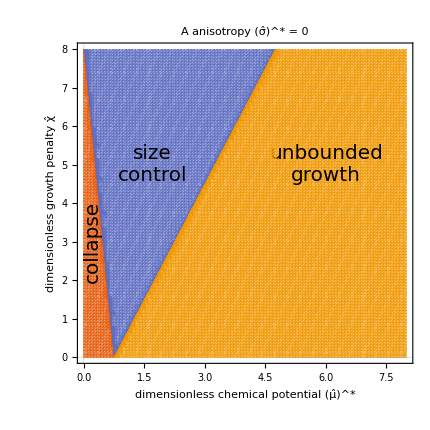

```mathematica
space="                       ";
zcoord=3;
RD=Show[CP, RP, Epilog->{Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{1.7,zcoord+2}], Inset[Style[Rotate["collapse", 90 Degree], FontFamily->"Times New Roman",  FontSlant->Italic, FontSize->20],{0.2,zcoord}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman",  FontSlant->Italic, FontSize->20],{6,zcoord+2}]}, 
PlotLabel->Style["A"<>space<>"anisotropy (σ̂)^* = 0"<>space, Black]]
```

## Realistic scenario

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

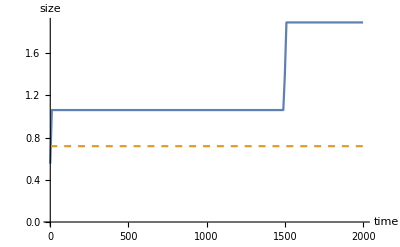
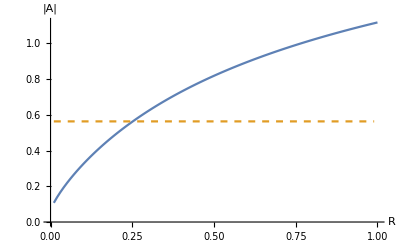
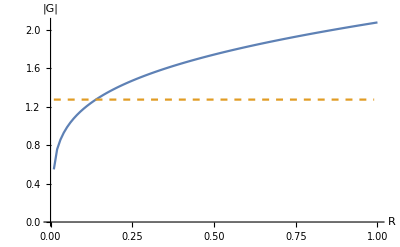
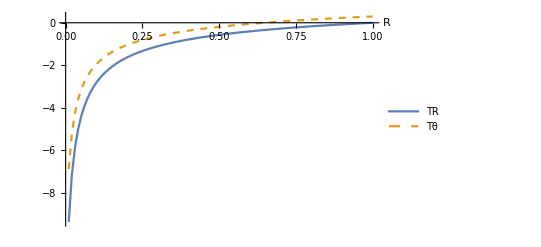

```mathematica
n=100; (* 100 *)
amp=0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=1500;
Pext=-1.0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=6.5;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=0.5*upperPsbound;

σ=0.15;



gInit=1//N;
tend=2000//N; (* 10 *)
range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;

{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetA[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|A|"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]}, Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}]
}
```

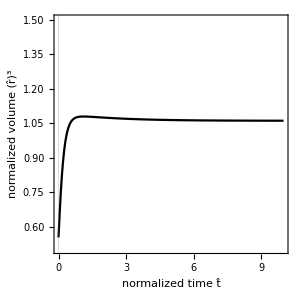

```mathematica
is=300;
bs=15;
tend=10;
P11=ListPlot[getSizeEvolution@sol1, Joined->True, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, PlotRange->{{0, tend},{All, 1.5}}, PlotStyle->Black, FrameLabel->{"normalized time t̂", "normalized   volume  (r̂)^3"}, Background->White]
```

```mathematica
tend=1000;
int=Interpolation@getSizeEvolution@sol1;
sizeFraction[frac_]:=tt/.FindRoot[frac==int[tt]/int[tend],{tt,0}]
fractions=Range[int[0]/int[tend], 1, 0.02];
range=Table[sizeFraction[frac],{frac,fractions}];

AppendTo[fractions, 1]; AppendTo[range, tend];

cols=colZeroOne/@fractions;
```

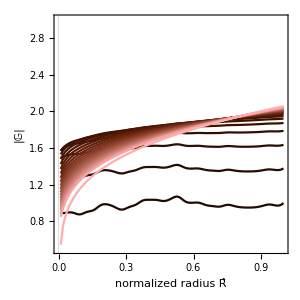

```mathematica
detGdata=getDetG[#, sol1]&/@range;
detAdata=getDetA[#, sol1]&/@range;

RP=RegionPlot[{ y≤1}, {x, 0, 1}, {y, 0, 1},AspectRatio->1, PlotTheme->"Scientific", PlotRange->{All,{0.5, 3}},BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "|𝔾|"},BoundaryStyle->None, PlotStyle->LightGray];

PlotDetA=ListPlot[detAdata, Joined->True, PlotRange->{All,All}, PlotStyle->cols, AspectRatio->1, PlotTheme->"Scientific", BaseStyle->0.8 bs, ImageSize->   is, FrameStyle->Black, FrameLabel->{None, "|𝔸|"}]; 


PlotDetG=ListPlot[detGdata, Joined->True, PlotRange->{All,{0.5, 3}},PlotStyle->cols, AspectRatio->1, PlotTheme->"Scientific", BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "|𝔾|"}];

P12=Show[ PlotDetG, Epilog->{Inset[PlotDetA,{0.3,2.4}, Automatic, 0.55]}, Background->White]
```

```mathematica
Tθdata=getTθ[#, sol1]&/@range;
TRdata=getTR[#, sol1]&/@range;
```

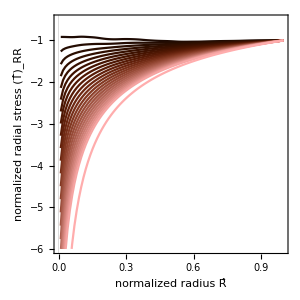

```mathematica
PlotHoopStress=ListPlot[Tθdata, Joined->True,  PlotStyle->cols, AspectRatio->1, PlotRange->{All,{-4, -0.5}}, PlotTheme->"Scientific", BaseStyle->0.8 bs, ImageSize->0.7 is, FrameStyle->Black,FrameLabel->{"R̂", "  (T̂)_θθ"}];

PlotRadialStress=ListPlot[TRdata, Joined->True,  PlotStyle->cols, AspectRatio->1, PlotRange->{All,{-6, -0.5}}, PlotRange->{All,All}, PlotTheme->"Scientific", BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "normalized  radial  stress  (T̂)_RR"}];

P21=PlotStresses=Show[%,Epilog->Inset[PlotHoopStress,{0.66,-4}, Automatic, 0.7], Background->White]
```

```mathematica
PlotBars=BarLegend[{colZeroOne,{0,1}}, LabelStyle->Directive[bs,Black,  FontFamily->"Times"], LegendLabel->Placed["size / final size", Right, Rotate[#,90 Degree]&], LegendLayout->"Column", ImageSize->2is, Background->White]
```

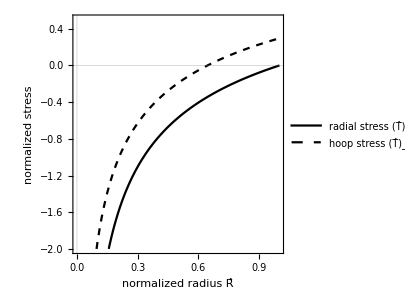

```mathematica
tendend=2000;

P22=ListPlot[{getTR[tendend, sol1], getTθ[tendend, sol1]}, Joined->True, PlotTheme->"Scientific", AspectRatio->1, ImageSize->is, BaseStyle->bs, FrameStyle->Black,  FrameLabel->{"normalized radius R̂", "normalized  stress"}, PlotStyle->{Black, Directive[Black, Dashed]}, PlotLegends->Placed[{"radial stress (T̂)_RR", "hoop stress (T̂)_θθ"},{Right, Bottom}], PlotRange->{All,{-2, 0.5}}, Background->White]
```

```mathematica
mytabLeft="          ";
mytabRight="   ";
textFirstRow=Style[#, FontFamily->"Times New Roman",1.2 bs, Black]&/@{"A"<>mytabLeft<>"size evolution"<>mytabRight<>"", "B"<>mytabLeft<>"   kinematic tensor evolution"<>mytabRight};
textSecondRow=Style[#, FontFamily->"Times New Roman",1.2 bs, Black]&/@{"C"<>mytabLeft<>" stress evolution"<>mytabRight<>"", "D"<>mytabLeft<>" residual stress"<>mytabRight};

spacingX=4;
spacingY=2;

GridTopRow=Grid[{textFirstRow, {P11, P12}}, Spacings->{spacingX, 1}];
GridBottomRow=Grid[{ textSecondRow, {P21, P22}}, Spacings->{spacingX, 1}];
Grid[{{GridTopRow}, {GridBottomRow}}, Spacings->{1, spacingY}];

Grid[{{ %, PlotBars}}, Spacings->{2, 1}, Background->White]
(*
Grid[{textFirstRow, {P11, P12, PlotBars}, te<3xtSecondRow, {P21, P22, ""}},Spacings->{4,{2->3,1.6}}]
*)
```

A          size evolution    | B             kinematic tensor evolution   
-Graphics- | -Graphics-
C           stress evolution    | D           residual stress   
-Graphics- | -Graphics- |

## Anisotropy data generation

```mathematica
solFUNSize[psArg_, χArg_]:=Module[{},
ps=psArg;
χ=χArg;
finalSize=1;
solTemp=First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,If[(r[n-1][t])^3>=100, finalSize=10^6, finalSize=0 ];"StopIntegration"]}/.gInit->1, vars, {t, 0, tend}]//Quiet;
If[finalSize==1, finalSize=(r[n-1][t])^3/.solTemp/.t->tend];
{{ps,χ },finalSize}

]
```

```mathematica
n=100;
amp= 0.0; (* noise amplitude *)

Pext=-1;
killGrowthTime=10^6;
PextEvolution[t_]:=Pext* killAt[t, 10^6];

κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;


gInit=1//N;
tend=10^4//N;

(*squareSize=0.025;*)
squareSize=1*0.5^2;
```

```mathematica
σ=-0.4;
AbsoluteTiming[data=Monitor[Table[tt=solFUNSize[psArg, χArg], {psArg,0,8, squareSize},{χArg, 0,8, squareSize}],tt];]
Export[ NotebookDirectory[]<>"export\\sigma_negative.mx",data]
```

InterpolatingFunction::dmval: Input value {10000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{9711.97,Null}

C:\Users\Alex\Dropbox\Sandbox\notebooks\ErlichRecho\notebooks\export\sigma_negative.mx

```mathematica
σ=0.15;
AbsoluteTiming[data=Monitor[Table[tt=solFUNSize[psArg, χArg], {psArg,0,8, squareSize},{χArg, 0,8, squareSize}],tt];]
Export[ NotebookDirectory[]<>"export\\sigma_positive.mx",data]
```

{6350.86,Null}

C:\Users\Alex\Dropbox\Sandbox\notebooks\ErlichRecho\notebooks\export\sigma_positive.mx

## Anisotropy import and plot

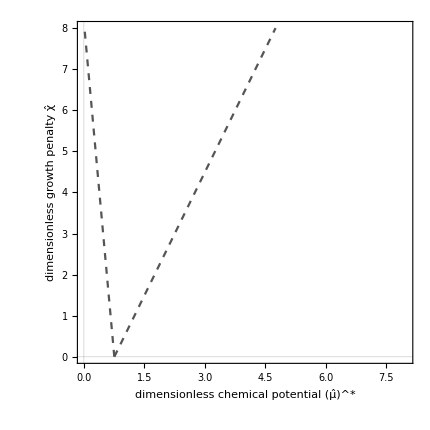

```mathematica
is= 430;
bs=17;
Jgrange=10;
μrange=8;

Pext=-1;
 μ=1;
κ=1;
Clear[ps, χ];

CP=ContourPlot[{rhsLower[ps, χ, Pext,μ, κ ]==0, rhsUpper[ps, χ, Pext,μ, κ ]==0}//Evaluate,{ps, 0, μrange}, {χ, 0, μrange}, PlotTheme->"Scientific", BaseStyle->bs, FrameStyle->Black, ContourStyle->Directive[Dashed, Darker@Gray],FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}, ImageSize->is]
```

```mathematica
colCollapse=RGBColor["#124961"]; colCollapse=RGBColor[0.9, 0.36, 0.054];
colSizeControl=RGBColor["#9a882b"]; colSizeControl=RGBColor[0.365248, 0.427802, 0.758297];
colUnbounded=RGBColor["#fcc2dd"]; colUnbounded=RGBColor[0.945109, 0.593901, 0.];
```

```mathematica
squareSize=1*0.5^2;

opa=0.6;
f=If[Last@#==0, {First@#, Directive[colCollapse, Opacity[opa]]}, If[Last@#==10^6, {First@#, Directive[colUnbounded, Opacity[opa]]}, {First@#, Directive[colSizeControl, Opacity[opa]]}]]&;

MakeSquare[input_]:=Module[{xpos, ypos},
{xpos, ypos}=First[input];
Graphics[ {Last@input, Rectangle[{xpos-squareSize/2, ypos-squareSize/2}, {xpos+squareSize/2, ypos+squareSize/2}]}]
]
```

### σ=0

```mathematica
data
```

data

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[data,1].

First::normal: Nonatomic expression expected at position 1 in First[data].

Set::shape: Lists {xpos$4985,ypos$4985} and First[data] are not the same shape.

Last::normal: Nonatomic expression expected at position 1 in Last[data].

First::normal: Nonatomic expression expected at position 1 in First[1].

Set::shape: Lists {xpos$5002,ypos$5002} and First[1] are not the same shape.

Last::normal: Nonatomic expression expected at position 1 in Last[1].

Flatten::flev: The level argument  in position 2 of Flatten[,] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Show::gtype: Flatten is not a type of graphics.

Flatten::flev: The level argument  in position 2 of Flatten[,] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Show::gtype: Flatten is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in ….

Show[Show[Flatten[-Graphics-,-Graphics-]],-Graphics-]

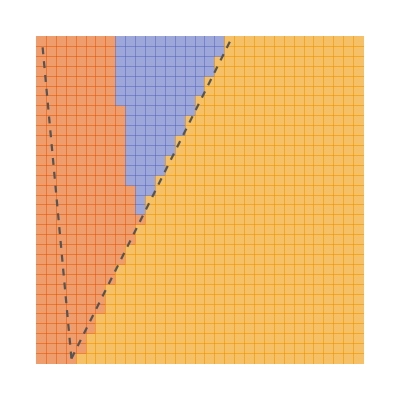

```mathematica
data=Import[ NotebookDirectory[]<>"export\\sigma_zero.mx"];
temp=Map[f, data, {2}];
PlotPixel=Show[MakeSquare/@Flatten[temp, 1]];
Show[PlotPixel, CP]
```

```mathematica
PlotPixel
```

Show[Flatten[-Graphics-,-Graphics-]]

```mathematica
ListContourPlot[Flatten[Map[Flatten, data, {2}], 1]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

ListContourPlot::arrayerr: Flatten[$Failed,1.] must be a valid array.

ListContourPlot[Flatten[$Failed,1]]

### σ<0

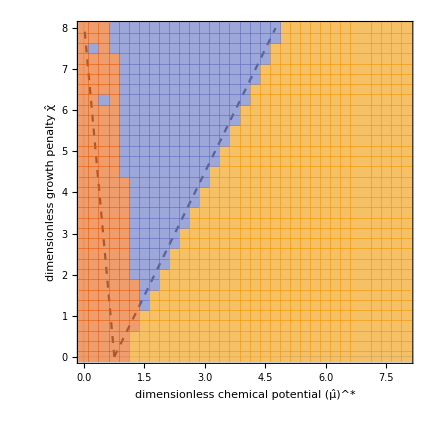

```mathematica
data=Import[ NotebookDirectory[]<>"export\\sigma_negative.mx"];
temp=Map[f, data, {2}];
PlotPixel=Show[MakeSquare/@Flatten[temp, 1]];
CPSigmaNegative=Show[CP, PlotPixel]
```

### σ>0

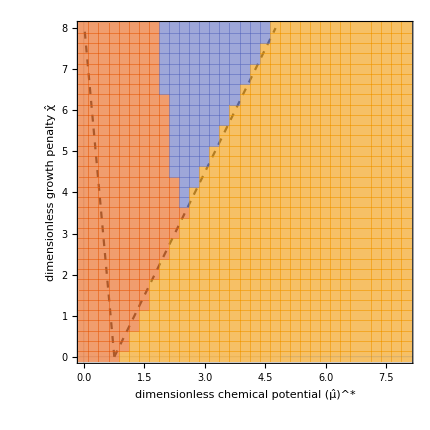

```mathematica
data=Import[ NotebookDirectory[]<>"export\\sigma_positive.mx"];
temp=Map[f, data, {2}];
PlotPixel=Show[MakeSquare/@Flatten[temp, 1]];
CPSigmaPositive=Show[ CP, PlotPixel]
```

## Anisotropy of homeostasis

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

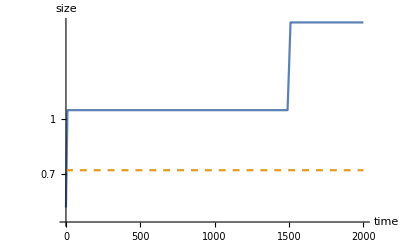
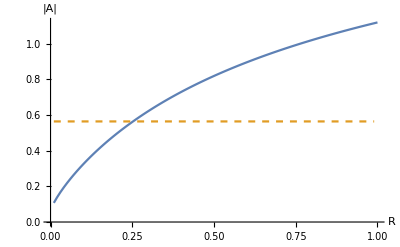
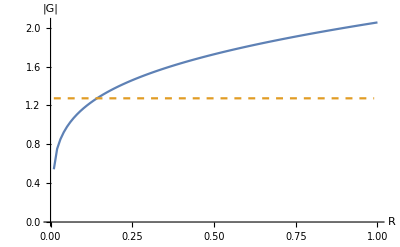
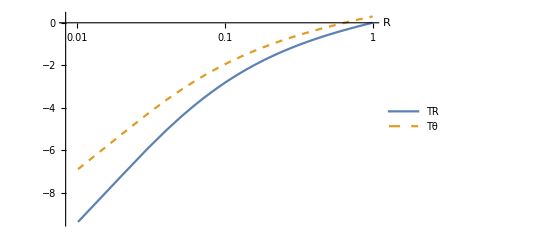

```mathematica
n=100;
amp= 0.0; (* noise amplitude *)

Pext=-1;
killGrowthTime=1000;
PextEvolution[t_]:=Pext* killAt[t,1500];

κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=6.5; 
Clear@ps;
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];

ps=Mean[{lowerPsbound, upperPsbound} ];
ps=0.8*upperPsbound;
ps=2.002;

σ=0.15;



gInit=1//N;
tend=2000//N;
range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;

jsxs=jsxsClassic;

sol1=solFUN[1]//Quiet;

{
ListLogPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetA[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|A|"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListLogLinearPlot[{getTR[tend, sol1], getTθ[tend, sol1]}, Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}]
}
```

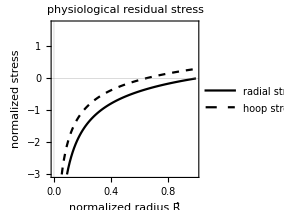

```mathematica
PPSigmaPositive=ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]}, PlotRange->{All,{-3, 1.7}},  Joined->True, PlotTheme->"Scientific", AspectRatio->1, ImageSize->210, BaseStyle->13, FrameStyle->Black,  FrameLabel->{"normalized radius R̂", "normalized  stress"}, PlotStyle->{Black, Directive[Black, Dashed]}, PlotLegends->Placed[{"radial stress (𝕋̂)_RR", "hoop stress (𝕋̂)_θθ"},{Left, Top}], PlotLabel->Style["physiological residual stress", Black]]
```

```mathematica
ps
```

2.002

```mathematica
χ
```

6.5

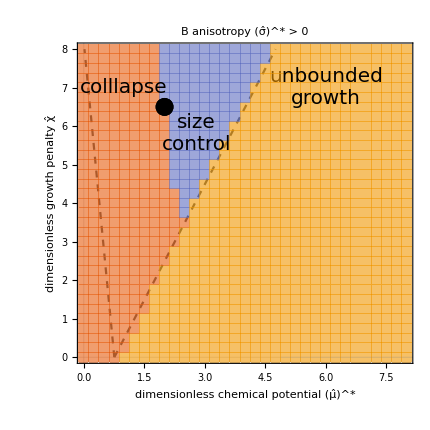

```mathematica
space="                       ";
zcoord=7;
LP=ListPlot[{{ps, χ}}, PlotStyle->Directive[Black, PointSize[0.03]]];
Plot1=Show[ CPSigmaPositive,  LP,  Epilog->{Inset[PPSigmaPositive,{5.5, 2.8}],Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{2.8,zcoord-1.2}], Inset[Style["colllapse", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{1,zcoord}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{6,zcoord}]}, PlotLabel->Style["B"<>space<>"anisotropy (σ̂)^* > 0"<>space, Black]]
```

```mathematica
{ps, χ}
```

{2.002,6.5}

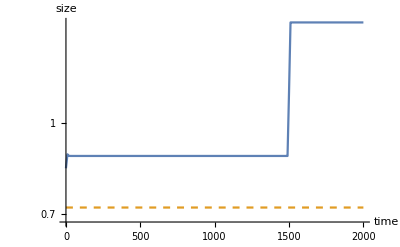
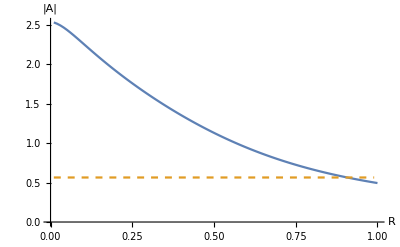
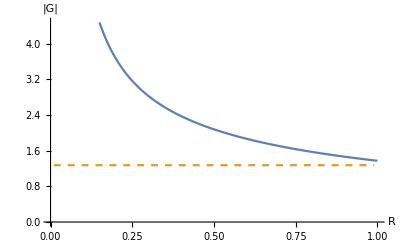
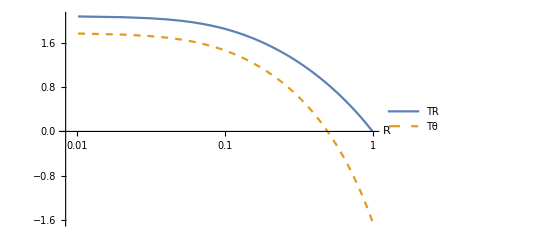

```mathematica
n=100;
amp= 0.0; (* noise amplitude *)

Pext=-1;
killGrowthTime=1000;
PextEvolution[t_]:=Pext* killAt[t,1500];

κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
ps=2;

Clear@ps;
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];

ps=Mean[{lowerPsbound, upperPsbound} ];
ps=0.8*upperPsbound;
ps=2.002;

σ=-0.4;



gInit=1//N;
tend=2000//N;
range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;

jsxs=jsxsClassic;

sol1=solFUN[1]//Quiet;

{
ListLogPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetA[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|A|"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListLogLinearPlot[{getTR[tend, sol1], getTθ[tend, sol1]}, Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}]
}
```

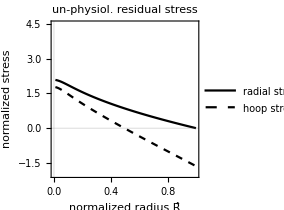

```mathematica
PPSigmaNegative=ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]}, PlotRange->{All, {-2,4.5}},  Joined->True, PlotTheme->"Scientific", AspectRatio->1, ImageSize->210, BaseStyle->13, FrameStyle->Black,  FrameLabel->{"normalized radius R̂", "normalized  stress"}, PlotStyle->{Black, Directive[Black, Dashed]}, PlotLegends->Placed[{"radial stress (𝕋̂)_RR", "hoop stress (𝕋̂)_θθ"},{Left, Top}], PlotLabel->Style["un-physiol. residual stress", Black]]
```

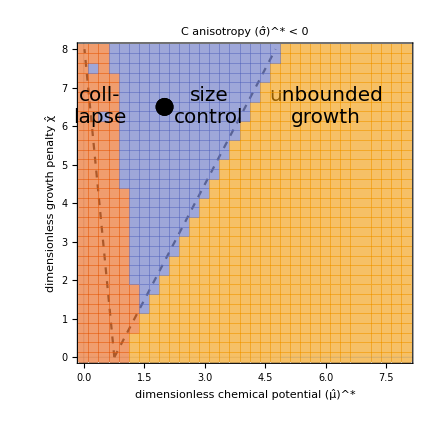

{2.002,6.5}

```mathematica
space="                       ";
zcoord=6.5;
LP=ListPlot[{{ps, χ}}, PlotStyle->Directive[Black, PointSize[0.03]]];
Plot2=Show[ CPSigmaNegative, LP, Epilog->{Inset[PPSigmaNegative,{5.5, 2.6}], Inset[Style["size\ncontrol", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{3.1,zcoord}], Inset[Style["coll-\nlapse", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{0.4,zcoord}], Inset[Style["unbounded\ngrowth", FontFamily->"Times New Roman", FontSlant->Italic, FontSize->20],{6,zcoord}]}, PlotLabel->Style["C"<>space<>"anisotropy (σ̂)^* < 0"<>space, Black]]
{ps, χ}
```

```mathematica
Grid[{{RD, SpanFromLeft},{Plot1, Plot2}}, Spacings->{4, 1}]
```

-Graphics- | 
-Graphics- | -Graphics-

## Animated gifs

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

```mathematica
colorMap=ColorMapSuite["vik"];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{"necrosis |OverHat[𝔾̇]| < 0 ","no change |OverHat[𝔾̇]| = 0", "growth |OverHat[𝔾̇]| > 0"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium]
```

### Unbounded growth

Power::infy: Infinite expression 1/0 encountered.

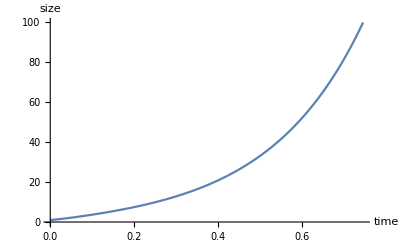
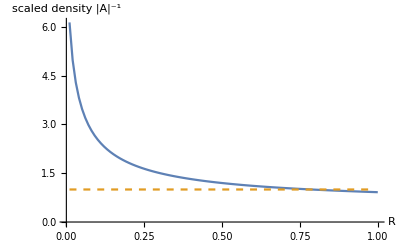
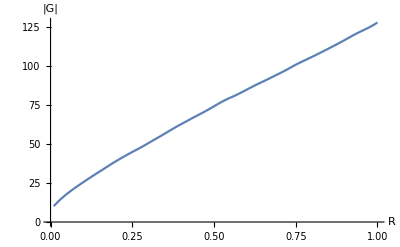
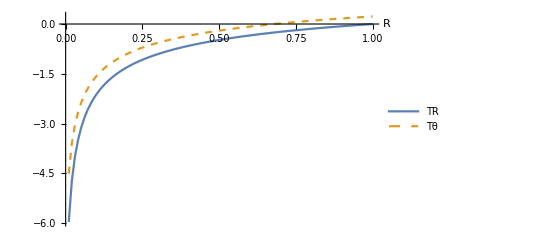
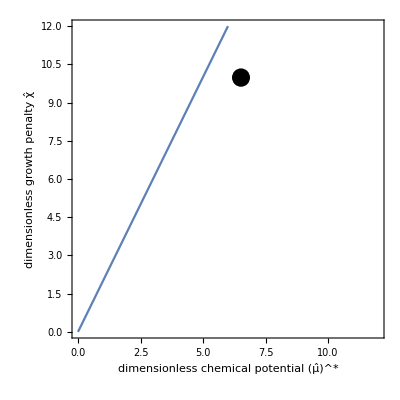
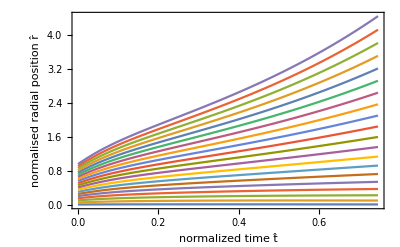
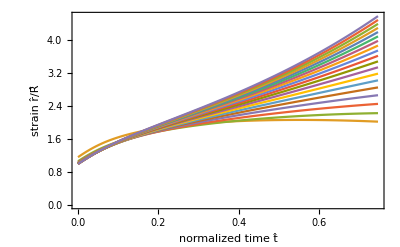

```mathematica
n=100; (* 100 *)
amp= 0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-3*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=10;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=6.5;
σ=0.08 ps;
tend=6//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;
temp=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, 1,n-1,5}];
tempStrain=Table[Table[{t,r[i][t]/((-1+i)/(-2+n))}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/100}],{i, 1,n-1,5}];
{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[temp, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]],
ListPlot[tempStrain, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "strain r̂/R̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
noOfPoints=80;
indexArray=RandomInteger[{1, n-1}, noOfPoints];
angleArray=RandomReal[{0, 2 Pi}, noOfPoints];

colorRange=10;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
(*BL=BarLegend[{colorMap,{0, 1}}, Legend]*)

Manipulate[
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.1 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["unbounded growth", 15]
]},{ BL}}],
{{tm, 0}, 0, tend}]
```

```mathematica
totalTime=4;
noOfImages=100;

CreateSingleImage[tm_]:=Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.1 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["unbounded growth", 15]
]},{ BL}}]
]
```

```mathematica
imageList=Table[CreateSingleImage[tm], {tm, 0,tend,tend/noOfImages }];
```

```mathematica
AbsoluteTiming[Export[NotebookDirectory[]<>"unbounded_growth.gif", imageList,"DisplayDurations"->totalTime/noOfImages, "AnimationRepetitions"->∞]]
```

{48.4592,C:\Users\alexa\Dropbox\Sandbox\notebooks\ErlichRecho\notebooks\unbounded_growth.gif}

### Stable growth

Power::infy: Infinite expression 1/0 encountered.

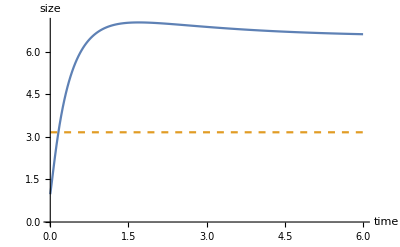
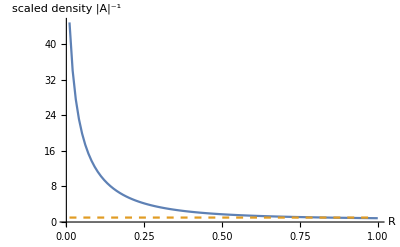
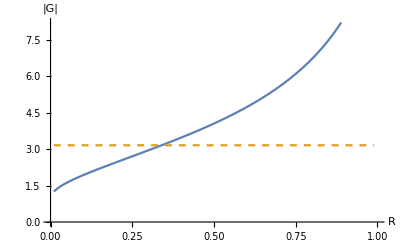
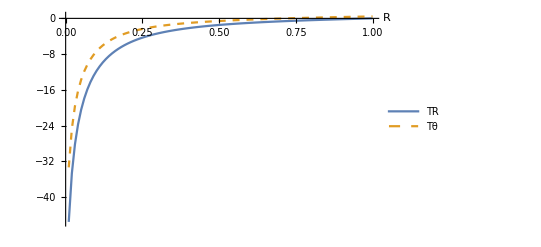
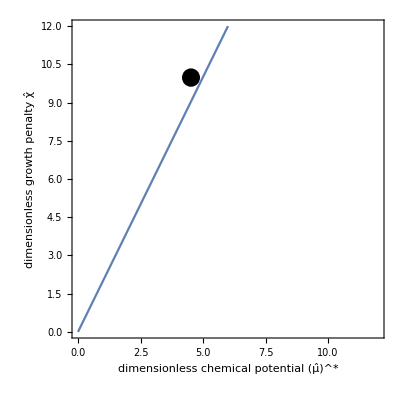
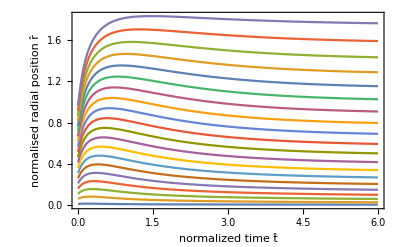
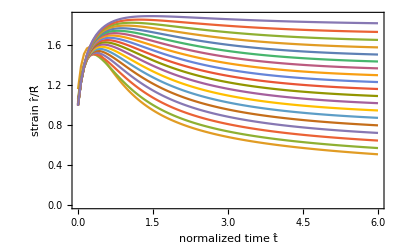

```mathematica
n=100; (* 100 *)
amp= 0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-3*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=10;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=4.5;
σ=0.08 ps;
tend=6//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;
temp=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, 1,n-1,5}];
tempStrain=Table[Table[{t,r[i][t]/((-1+i)/(-2+n))}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/100}],{i, 1,n-1,5}];
{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[temp, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]],
ListPlot[tempStrain, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "strain r̂/R̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
noOfPoints=80;
indexArray=RandomInteger[{1, n-1}, noOfPoints];
angleArray=RandomReal[{0, 2 Pi}, noOfPoints];

colorRange=0.2 0.5;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
(*BL=BarLegend[{colorMap,{0, 1}}, Legend]*)

Manipulate[
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],1.1positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.1 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["stable growth", 15]
]},{ BL}}],
{{tm, 0}, 0, tend}]
```

```mathematica
totalTime=4;
noOfImages=100;

CreateSingleImage[tm_]:=Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.1 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["stable growth", 15]
]},{ BL}}]
]
```

```mathematica
tm
```

tm

```mathematica
imageList=Table[CreateSingleImage[tm], {tm, 0,tend,tend/noOfImages }];
```

```mathematica
imageList[[-1]]
```

-Graphics-

```mathematica
AbsoluteTiming[Export[NotebookDirectory[]<>"stable_growth.gif", imageList,"DisplayDurations"->totalTime/noOfImages, "AnimationRepetitions"->∞]]
```

{74.1553,C:\Users\alexa\Dropbox\Sandbox\notebooks\ErlichRecho\notebooks\stable_growth.gif}

### Collapse

Power::infy: Infinite expression 1/0 encountered.

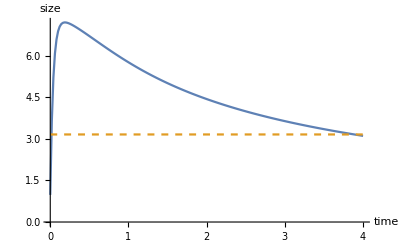
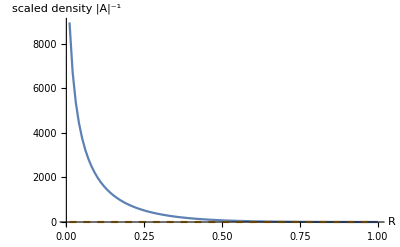
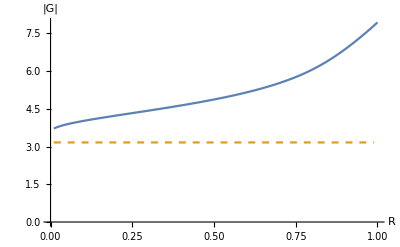
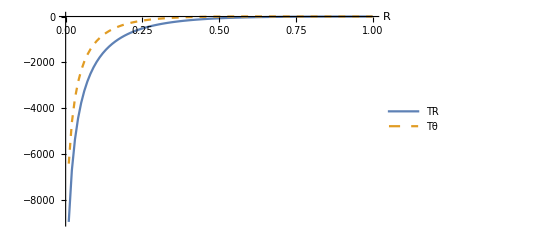
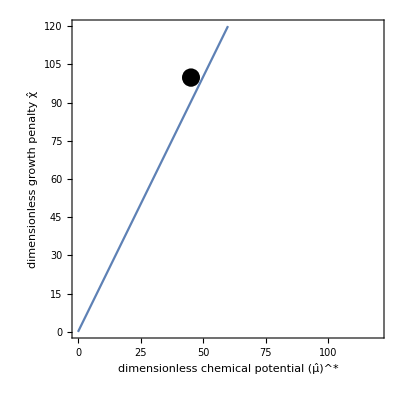
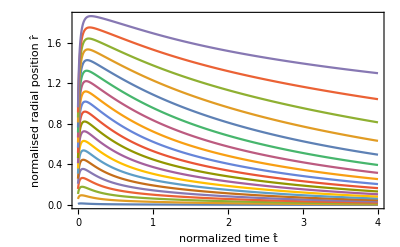
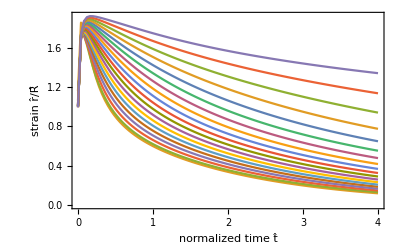

```mathematica
n=100; (* 100 *)
amp= 0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-3*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=100;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=45;
σ=0.03 ps;
tend=4//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;
temp=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, 1,n-1,5}];
tempStrain=Table[Table[{t,r[i][t]/((-1+i)/(-2+n))}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/100}],{i, 1,n-1,5}];
{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[temp, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]],
ListPlot[tempStrain, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "strain r̂/R̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
noOfPoints=80;
indexArray=RandomInteger[{1, n-1}, noOfPoints];
angleArray=RandomReal[{0, 2 Pi}, noOfPoints];

colorRange=0.2 0.5;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
(*BL=BarLegend[{colorMap,{0, 1}}, Legend]*)

Manipulate[
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.3 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["collapse", 15]
]},{ BL}}],
{{tm, 0}, 0, tend}]
```

```mathematica
totalTime=4;
noOfImages=100;

CreateSingleImage[tm_]:=Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Grid[{{Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{positionArray[[k,2]],positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[White]], Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.02]}, {k, 1, noOfPoints}]},PlotRange->1.3 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->Style["collapse", 15]
]},{ BL}}]
]
```

```mathematica
tm
```

tm

```mathematica
imageList=Table[CreateSingleImage[tm], {tm, 0,tend,tend/noOfImages }];
```

```mathematica
imageList[[-1]]
```

-Graphics-

```mathematica
AbsoluteTiming[Export[NotebookDirectory[]<>"collapse.gif", imageList,"DisplayDurations"->totalTime/noOfImages, "AnimationRepetitions"->∞]]
```

{61.5213,C:\Users\alexa\Dropbox\Sandbox\notebooks\ErlichRecho\notebooks\collapse.gif}

### Old

```mathematica
OverHat[t]
```

t̂

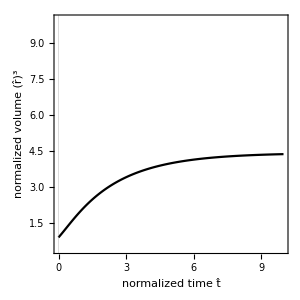

```mathematica
is=300;
bs=15;
tend=10;
P11=ListPlot[getSizeEvolution@sol1, Joined->True, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, PlotRange->{{0, tend},{All,10}}, PlotStyle->Black, FrameLabel->{"normalized time t̂", "normalized   volume  (r̂)^3"}, Background->White]
```

```mathematica
tend=1000;
int=Interpolation@getSizeEvolution@sol1;
sizeFraction[frac_]:=tt/.FindRoot[frac==int[tt]/int[tend],{tt,0}]
fractions=Range[int[0]/int[tend], 1, 0.02];
range=Table[sizeFraction[frac],{frac,fractions}];

AppendTo[fractions, 1]; AppendTo[range, tend];

cols=colZeroOne/@fractions;
```

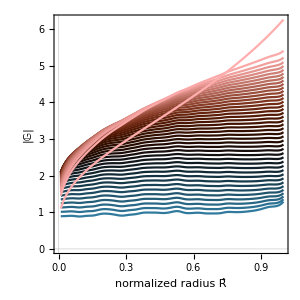

```mathematica
detGdata=getDetG[#, sol1]&/@range;
detAdata=getDetA[#, sol1]&/@range;

RP=RegionPlot[{ y≤1}, {x, 0, 1}, {y, 0, 1},AspectRatio->1, PlotTheme->"Scientific", PlotRange->{All,{0.5, 3}},BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "|𝔾|"},BoundaryStyle->None, PlotStyle->LightGray];

PlotDetA=ListPlot[detAdata, Joined->True, PlotRange->{All,All}, PlotStyle->cols, AspectRatio->1, PlotTheme->"Scientific", BaseStyle->0.8 bs, ImageSize->   is, FrameStyle->Black, FrameLabel->{None, "|𝔸|"}]; 


PlotDetG=ListPlot[detGdata, Joined->True,PlotRange->All, PlotRange->{All,{0.5, 3}},PlotStyle->cols, AspectRatio->1, PlotTheme->"Scientific", BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "|𝔾|"}];

P12=Show[ PlotDetG, Epilog->{Inset[PlotDetA,{0.3,2.4}, Automatic, 0.55]}, Background->White]
```

```mathematica
Tθdata=getTθ[#, sol1]&/@range;
TRdata=getTR[#, sol1]&/@range;
```

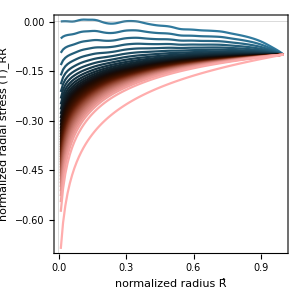

```mathematica
PlotHoopStress=ListPlot[Tθdata, Joined->True,  PlotStyle->cols, AspectRatio->1,PlotRange->All,  PlotRange->{All,{-4, -0.5}}, PlotTheme->"Scientific", BaseStyle->0.8 bs, ImageSize->0.7 is, FrameStyle->Black,FrameLabel->{"R̂", "  (T̂)_θθ"}];

PlotRadialStress=ListPlot[TRdata, Joined->True,  PlotStyle->cols, AspectRatio->1,PlotRange->All,  PlotRange->{All,{-6, -0.5}}, PlotRange->{All,All}, PlotTheme->"Scientific", BaseStyle->bs, ImageSize-> is, FrameStyle->Black, FrameLabel->{"normalized radius R̂", "normalized  radial  stress  (T̂)_RR"}];

P21=PlotStresses=Show[%,Epilog->Inset[PlotHoopStress,{0.66,-0.4}, Automatic, 0.7], Background->White]
```

```mathematica
PlotBars=BarLegend[{colZeroOne,{0,1}}, LabelStyle->Directive[bs,Black,  FontFamily->"Times"], LegendLabel->Placed["size / final size", Right, Rotate[#,90 Degree]&], LegendLayout->"Column", ImageSize->2is, Background->White]
```

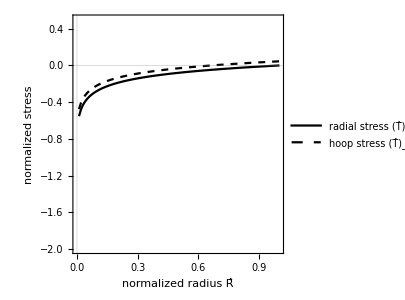

```mathematica
tendend=2000;

P22=ListPlot[{getTR[tendend, sol1], getTθ[tendend, sol1]}, Joined->True, PlotTheme->"Scientific", AspectRatio->1, ImageSize->is, BaseStyle->bs, FrameStyle->Black,  FrameLabel->{"normalized radius R̂", "normalized  stress"}, PlotStyle->{Black, Directive[Black, Dashed]}, PlotLegends->Placed[{"radial stress (T̂)_RR", "hoop stress (T̂)_θθ"},{Right, Bottom}], PlotRange->{All,{-2, 0.5}}, Background->White]
```

```mathematica
mytabLeft="          ";
mytabRight="   ";
textFirstRow=Style[#, FontFamily->"Times New Roman",1.2 bs, Black]&/@{"A"<>mytabLeft<>"size evolution"<>mytabRight<>"", "B"<>mytabLeft<>"   kinematic tensor evolution"<>mytabRight};
textSecondRow=Style[#, FontFamily->"Times New Roman",1.2 bs, Black]&/@{"C"<>mytabLeft<>" stress evolution"<>mytabRight<>"", "D"<>mytabLeft<>" residual stress"<>mytabRight};

spacingX=4;
spacingY=2;

GridTopRow=Grid[{textFirstRow, {P11, P12}}, Spacings->{spacingX, 1}];
GridBottomRow=Grid[{ textSecondRow, {P21, P22}}, Spacings->{spacingX, 1}];
Grid[{{GridTopRow}, {GridBottomRow}}, Spacings->{1, spacingY}];

Grid[{{ %, PlotBars}}, Spacings->{2, 1}, Background->White]
(*
Grid[{textFirstRow, {P11, P12, PlotBars}, te<3xtSecondRow, {P21, P22, ""}},Spacings->{4,{2->3,1.6}}]
*)
```

A          size evolution    | B             kinematic tensor evolution   
-Graphics- | -Graphics-
C           stress evolution    | D           residual stress   
-Graphics- | -Graphics- |

## Necrotic core

### bounded growth

```mathematica
colorMap=ColorMapSuite["vik"];
{necroticColor, growingColor}={colorMap[0.45], colorMap[0.55]}
```

{RGBColor[0.8101248623471478, 0.8773109778172077, 0.9100007045130043],RGBColor[0.9230684275871923, 0.8196072507518759, 0.7602966126424823]}

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

```mathematica
colorMap=ColorMapSuite["vik"];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{"necrosis |OverHat[𝔾̇]| < 0 ","no change |OverHat[𝔾̇]| = 0", "growth |OverHat[𝔾̇]| > 0"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium]
```

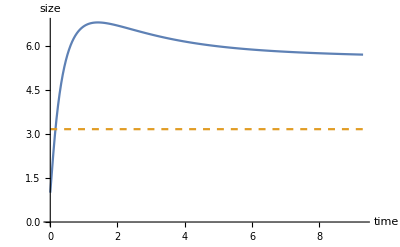
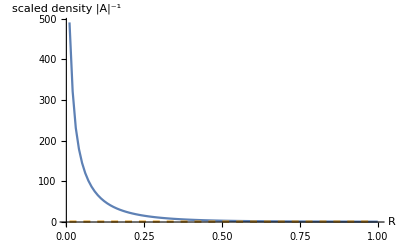
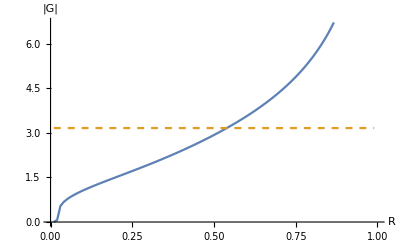
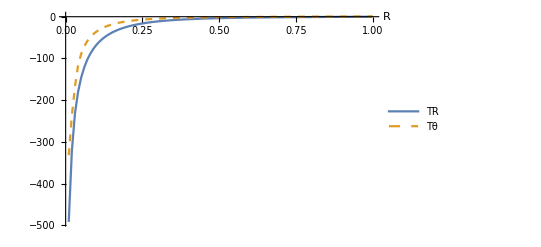
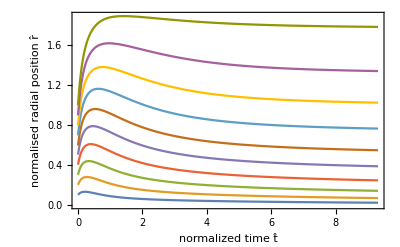
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
n=100; (* 100 *)
amp= 0*0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-0.5*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=10;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=4.5;
σ=0.11ps;
tend=50//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1];
materialPoints=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, Floor[Subdivide[1, n-1,10][[2;;-1]]]}];

{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[materialPoints, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
necroticRadius[tm_]:=Module[{},
detGDotArray=Table[{r[k][t],((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)}/.sol1/.t->tm, {k, 1, n-1}];
rnecrotic=0;
If[Sign[detGDotArray[[1,2]]]*Sign[detGDotArray[[-1,2]]]==-1, interp=Interpolation[detGDotArray];
rnecrotic=r/.FindRoot[interp[r]==0,{r, 1}];];
rnecrotic
]

timepoints=200;
necroticRadiusData=Table[{t, necroticRadius[t]},{t,  0, tend, tend/timepoints}]//Quiet;
```

```mathematica
Filling
```

Filling

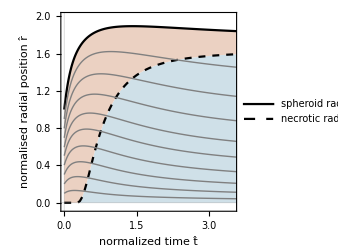

```mathematica
is=250;
bs=15;
tendPlot=3.5;
LPSize=ListPlot[{materialPoints[[-1]], necroticRadiusData}, Joined->True,Frame->True,  PlotRange->{{0, tendPlot},{-0.05, 2}}, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, PlotStyle->{Black,Directive[Black, Dashed]}, FrameLabel->{"normalized time t̂", "normalised radial position r̂"}, Filling->{{1->{{2},growingColor}}, 2->{Axis, necroticColor}}, PlotLegends->Placed[{"spheroid radius", "necrotic radius"},{Right, Bottom}]];
(*LPnecrotic=ListPlot[necroticRadiusData, Joined->True, PlotStyle->Directive[Black, Dashed]];*)
LPintermediate=ListPlot[materialPoints[[1;;-2]], Joined->True, PlotStyle->Directive[Thin,Gray]];
PP=Show[LPSize,LPintermediate ]
```

```mathematica
Clear@timeString
```

```mathematica
norm[vec_]:=√(vec.vec)
anglecalc[vec1_,vec2_]:=Mod[(ArcTan@@vec2)-(ArcTan@@vec1),2 π] (* signed vector angle *)
```

```mathematica
findNearestIndex[rad_]:=First@Nearest[Table[r[k][t]/.sol1/.t->0,{k, 1, n-1}]->Table[k,{k, 1, n-1}], rad]
```

```mathematica
noOfPoints=100;
pts=RandomPoint[Disk[{0, 0}, 0.95],noOfPoints];
indexArray=findNearestIndex/@(norm/@pts);
angleArray=anglecalc[#,{1, 0}]&/@pts;

colorRange=0.2 0.5;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{ToString[-colorRange]<>"\nnecrosis",0, ToString[colorRange]<>"\ngrowth"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium, LegendLabel->"|OverHat[𝔾̇]||𝔾|^-1"];
timeString[tm_]:=Style["t̂="<>ToString[tm], 30]

CreateSingleImage[tm_]:=Rasterize@Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal= 1.1(r[n-1][t]/.sol1/.t->tend);
Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{0.99positionArray[[k,2]],1.01positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[Black]],White,  Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.04]}, {k, 1, noOfPoints}]},PlotRange->1.1 radiusFinal{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->timeString[tm]]]
mygrid=Grid[Transpose@{CreateSingleImage/@{0,0.6,  3,8.5}}];
gridBounded=Grid[{{PP},{ mygrid},{BL}}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### collapse

```mathematica
colorMap=ColorMapSuite["vik"];
{necroticColor, growingColor}={colorMap[0.45], colorMap[0.55]}
```

{RGBColor[0.8101248623471478, 0.8773109778172077, 0.9100007045130043],RGBColor[0.9230684275871923, 0.8196072507518759, 0.7602966126424823]}

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

```mathematica
colorMap=ColorMapSuite["vik"];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{"necrosis |OverHat[𝔾̇]| < 0 ","no change |OverHat[𝔾̇]| = 0", "growth |OverHat[𝔾̇]| > 0"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium]
```

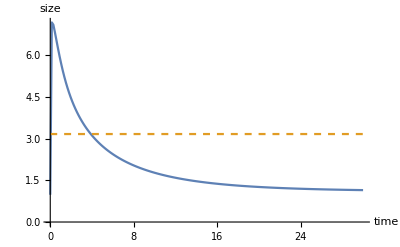
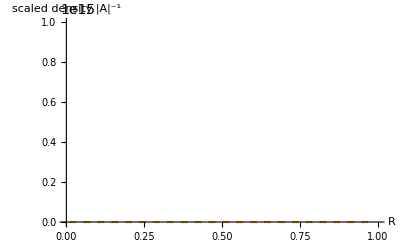
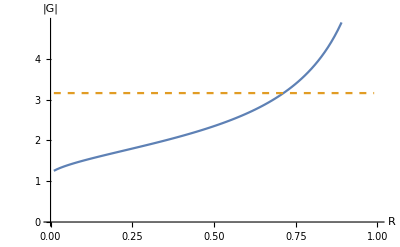
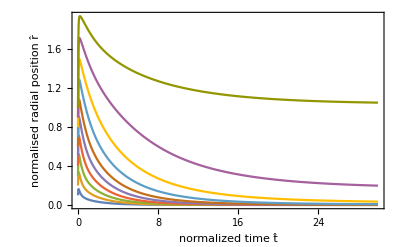
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
n=100; (* 100 *)
amp= 0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-3*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=100;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=45;
σ=0.03 ps;
tend=30//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;
materialPoints=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, Floor[Subdivide[1, n-1,10][[2;;-1]]]}];

{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[materialPoints, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
necroticRadius[tm_]:=Module[{},
detGDotArray=Table[{r[k][t],((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)}/.sol1/.t->tm, {k, 1, n-1}];
rnecrotic=0;
If[Sign[detGDotArray[[1,2]]]*Sign[detGDotArray[[-1,2]]]==-1, interp=Interpolation[detGDotArray];
rnecrotic=r/.FindRoot[interp[r]==0,{r, 1}];];
rnecrotic
]

tendPlot=2;
timepoints=200;
necroticRadiusData=Table[{t, necroticRadius[t]},{t,  0, tendPlot, tendPlot/timepoints}]//Quiet;
materialPoints=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tendPlot, tendPlot/200}],{i, Floor[Subdivide[1, n-1,10][[2;;-1]]]}];
```

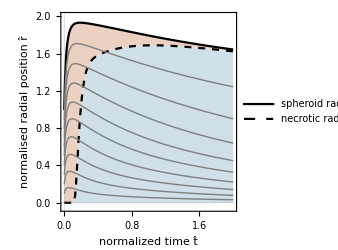

```mathematica
is=250;
bs=15;

LPSize=ListPlot[{materialPoints[[-1]], necroticRadiusData}, Joined->True,Frame->True,  PlotRange->{{0, tendPlot},{-0.05, 2}}, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, PlotStyle->{Black,Directive[Black, Dashed]}, FrameLabel->{"normalized time t̂", "normalised radial position r̂"}, Filling->{{1->{{2},growingColor}}, 2->{Axis, necroticColor}}, PlotLegends->Placed[{"spheroid radius", "necrotic radius"},{Right, Bottom}]];
(*LPnecrotic=ListPlot[necroticRadiusData, Joined->True, PlotStyle->Directive[Black, Dashed]];*)
LPintermediate=ListPlot[materialPoints[[1;;-2]], Joined->True, PlotStyle->Directive[Thin,Gray]];
PP=Show[LPSize,LPintermediate ]
```

```mathematica
norm[vec_]:=√(vec.vec)
anglecalc[vec1_,vec2_]:=Mod[(ArcTan@@vec2)-(ArcTan@@vec1),2 π] (* signed vector angle *)
```

```mathematica
findNearestIndex[rad_]:=First@Nearest[Table[r[k][t]/.sol1/.t->0,{k, 1, n-1}]->Table[k,{k, 1, n-1}], rad]
```

```mathematica
noOfPoints=100;
pts=RandomPoint[Disk[{0, 0}, 0.95],noOfPoints];
indexArray=findNearestIndex/@(norm/@pts);
angleArray=anglecalc[#,{1, 0}]&/@pts;

colorRange=0.2 0.5;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{ToString[-colorRange]<>"\nnecrosis",0, ToString[colorRange]<>"\ngrowth"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium, LegendLabel->"|OverHat[𝔾̇]||𝔾|^-1"];
timeString[tm_]:=Style["t̂="<>ToString[tm], 30]

CreateSingleImage[tm_]:=Rasterize@Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal=1(r[n-1][t]/.sol1/.t->tend);
Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{0.99positionArray[[k,2]],1.01positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[Black]],White,  Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.04]}, {k, 1, noOfPoints}]},PlotRange->2.0{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->timeString[tm]]]
mygrid=Grid[Transpose@{CreateSingleImage/@{0,0.15,1,15}}];
gridCollapse=Grid[{{PP},{ mygrid},{BL}}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### unbouned growth

```mathematica
colorMap=ColorMapSuite["vik"];
{necroticColor, growingColor}={colorMap[0.45], colorMap[0.55]}
```

{RGBColor[0.8101248623471478, 0.8773109778172077, 0.9100007045130043],RGBColor[0.9230684275871923, 0.8196072507518759, 0.7602966126424823]}

```mathematica
solFUN[gInitp_]:=Module[{},
Clear[gInit];
First@NDSolve[{ODEs, BCs, ICs, WhenEvent[(r[n-1][t])^3>100||(r[n-1][t])^3<0.1||γR[n-1][t](γθ[n-1][t])^2<10^-10||γR[1][t](γθ[1][t])^2<10^-10//Evaluate,tend=t;"StopIntegration"]}/.gInit->gInitp, vars, {t, 0, tend}]]
```

```mathematica
colorMap=ColorMapSuite["vik"];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{"necrosis |OverHat[𝔾̇]| < 0 ","no change |OverHat[𝔾̇]| = 0", "growth |OverHat[𝔾̇]| > 0"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium]
```

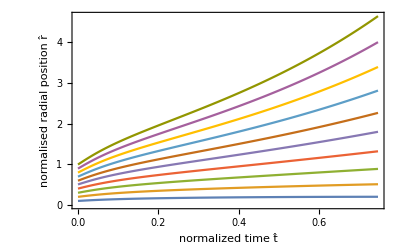
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
n=100; (* 100 *)
amp= 0.03575; (* noise amplitude *)
killAt[t_, KillTime_]:=0.5+-0.5Tanh[10^2(t-KillTime)]
killGrowthTime=10^6;
Pext=-3*0;
PextEvolution[t_]:=Pext* killAt[t,killGrowthTime];
κ=1//N; (* the higher, the closer to incompressibility *)
μ=1//N;
B=1//N;
χ=10;  (* 6.5 *)
Clear[ps]
upperPsbound=ps/.First@Solve[0==rhsLower[ps, χ, Pext,μ, κ ], ps];
lowerPsbound=ps/.First@Solve[0==rhsUpper[ps, χ, Pext,μ, κ ], ps];
(*ps=Mean[{lowerPsbound, upperPsbound} ];*)
ps=6.5;
σ=0.08 ps;
tend=6//N; (* 10 *)

gInit=1//N;

range=10^Range[-4, Log10[tend],(Log10[tend]+4)/(10-1)];
colFun=batlowBlend[#/tend]&;
cols=colFun/@range;
μrange=1.2Max[χ, ps];

jsxs=jsxs2;

sol1=solFUN[1]//Quiet;
materialPoints=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tend, tend/1000}],{i, Floor[Subdivide[1, n-1,10][[2;;-1]]]}];

{
ListPlot[{getSizeEvolution@sol1, getSizeExact[Pext,κ ]}, PlotRange->{All, {0, Automatic}}, Joined->True, AxesLabel->{"time", "size"}, PlotStyle->{Automatic, Dashed}],
ListPlot[{getDensity[tend, sol1], getDetAExact[Pext, κ]}//Evaluate, Joined->True,PlotRange->All, AxesLabel->{"R", "scaled density |A|^-1"},  PlotStyle->{Automatic, Dashed}],
ListPlot[{getDetG[tend, sol1], getDetGExact[Pext, κ]}//Evaluate, Joined->True, AxesLabel->{"R", "|G|"},  PlotStyle->{Automatic, Dashed}], 
ListPlot[{getTR[tend, sol1], getTθ[tend, sol1]} ,Joined->True, AxesLabel->{"R", None}, PlotRange->All, PlotLegends->Placed[{"TR", "Tθ"},{Top,Right}], PlotStyle->{Automatic, Dashed}],
Show[ContourPlot[{rhsLower[psparam, χparam, Pext,μ, κ ]==0, rhsUpper[psparam, χparam, Pext,μ, κ ]==0}//Evaluate,{psparam, 0, μrange}, {χparam, 0, μrange},FrameLabel->{"dimensionless chemical potential (μ̂)^*", "dimensionless growth  penalty χ̂"}],Graphics[Disk[{ps, χ},0.03μrange]]],
ListPlot[materialPoints, Joined->True,Frame->True,FrameLabel->{"normalized time t̂", "normalised radial position r̂"},  PlotRange->All, AxesLabel->"Pext = "<>ToString[Pext]]
}
```

```mathematica
necroticRadius[tm_]:=Module[{},
detGDotArray=Table[{r[k][t],((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)}/.sol1/.t->tm, {k, 1, n-1}];
rnecrotic=0;
If[Sign[detGDotArray[[1,2]]]*Sign[detGDotArray[[-1,2]]]==-1, interp=Interpolation[detGDotArray];
rnecrotic=r/.FindRoot[interp[r]==0,{r, 1}];];
rnecrotic
]

tendPlot=1.5;
timepoints=200;
necroticRadiusData=Table[{t, necroticRadius[t]},{t,  0, tendPlot, tendPlot/timepoints}]//Quiet;
materialPoints=Table[Table[{t,r[i][t](*/((-1+i)/(-2+n))*)}/.sol1/.t->tt//Evaluate, {tt, 0, tendPlot, tendPlot/200}],{i, Floor[Subdivide[1, n-1,10][[2;;-1]]]}];
```

InterpolatingFunction::dmval: Input value {0.75} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.7575} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.765} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

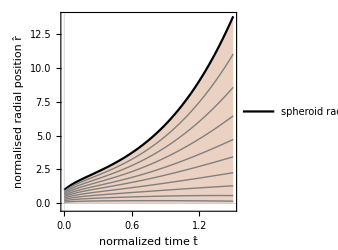

```mathematica
is=250;
bs=15;

LPSize=ListPlot[{materialPoints[[-1]]}, Joined->True,Frame->True,  PlotRange->{{0, tendPlot},{-0.3,Automatic}}, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->bs, ImageSize->is, FrameStyle->Black, PlotStyle->{Black,Directive[Black, Dashed]}, FrameLabel->{"normalized time t̂", "normalised radial position r̂"}, Filling->Axis,FillingStyle->growingColor, PlotLegends->Placed[{"spheroid radius"},{Left, Top}]];
(*LPnecrotic=ListPlot[necroticRadiusData, Joined->True, PlotStyle->Directive[Black, Dashed]];*)
LPintermediate=ListPlot[materialPoints[[1;;-2]], Joined->True, PlotStyle->Directive[Thin,Gray]];
PP=Show[LPSize,LPintermediate ]
```

```mathematica
norm[vec_]:=√(vec.vec)
anglecalc[vec1_,vec2_]:=Mod[(ArcTan@@vec2)-(ArcTan@@vec1),2 π] (* signed vector angle *)
```

```mathematica
findNearestIndex[rad_]:=First@Nearest[Table[r[k][t]/.sol1/.t->0,{k, 1, n-1}]->Table[k,{k, 1, n-1}], rad]
```

```mathematica
noOfPoints=100;
pts=RandomPoint[Disk[{0, 0}, 0.95],noOfPoints];
indexArray=findNearestIndex/@(norm/@pts);
angleArray=anglecalc[#,{1, 0}]&/@pts;

colorRange=10;
colorMapAdapted[val_]:=colorMap[1/2+val/(2 colorRange)];
```

```mathematica
BL=BarLegend[{colorMap,{0,1}}, "Ticks"->{0,0.5,1},"TickLabels"->{ToString[-colorRange]<>"\nnecrosis",0, ToString[colorRange]<>"\ngrowth"}, LegendLayout->"Row", ImageSize->300, LabelStyle->Medium, LegendLabel->"|OverHat[𝔾̇]||𝔾|^-1"];
timeString[tm_]:=Style["t̂="<>ToString[tm], 30]

CreateSingleImage[tm_]:=Rasterize@Module[{},
positionArray=getr[tm, sol1];
detGDotArray=Table[((γθ[k][t])^2 γR[k]'[t]+2 γR[k][t] γθ[k][t] γθ[k]'[t])/(γR[k][t](γθ[k][t])^2)/.sol1/.t->tm, {k, 1, n-1}];
radiusFinal=1(r[n-1][t]/.sol1/.t->tend);
Graphics[{
Table[{colorMapAdapted[detGDotArray[[k]]], Annulus[{0,0},{0.99positionArray[[k,2]],1.01positionArray[[k+1,2]] }]},{k,2, n-2}  ], 
Table[{EdgeForm[Directive[Black]],White,  Disk[( r[indexArray[[k]]][t]/.sol1/.t->tm){Cos[angleArray[[k]]], Sin[angleArray[[k]]]},  0.04]}, {k, 1, noOfPoints}]},PlotRange->3{{-1, 1}, {-1, 1}}, ImageSize->400, PlotLabel->timeString[tm]]]
mygrid=Grid[Transpose@{CreateSingleImage/@{0,0.1,0.2,0.4}}];
gridUnbounded=Grid[{{PP},{ mygrid},{BL}}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### plot them together

```mathematica
Grid[{{gridBounded, gridCollapse, gridUnbounded}}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
 | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
 | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## DensityPlot Spheroid visualisation

```mathematica
myColorFunction[val_]:=colZeroOne[1/2+val/(2 valRange)]
```

```mathematica
valRange=0.15;
```

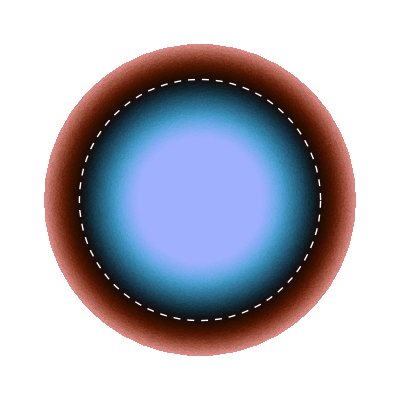

```mathematica
NecroticRadius=necroticRadius[2];
TotalRadius=detGDotArray[[-1,1]];
interp=Interpolation[detGDotArray];
necroticCircle=Graphics[{White, Dashed, Circle[{0, 0},NecroticRadius]}];
reg=Disk[{0, 0},TotalRadius];
DP=DensityPlot[interp[√(x^2+y^2)],{x,y}∈reg, ColorFunction->myColorFunction, PlotPoints->100,  ColorFunctionScaling->False, PlotRange->2{{-1,1}, {-1,1}}, Frame->False];
Show[DP, necroticCircle]
```